## Import Xueqi’s code on MassMatrix

```mathematica
(*Basic Definition*)
MakeMatrix[n_]:=Table[n[i,j],{i,1,3},{j,1,3}]; (*Make a matrix with element n[i,j]*)
Dagger[x_]:=Transpose[x]//Conjugate//Simplify; 
ω=E^(2 Pi I/3); (*ST Fixed Point*)
ListToString[list_]:=StringJoin[ToString/@list];
(*Convert output to display form*)
MatrixDisplayRule={m0[x_,y_]:>Subscript[Superscript[m,0],{x,y}//ListToString],m01[x_,y_]:>Subscript[Superscript[m,"01"],{x,y}//ListToString],m10[x_,y_]:>Subscript[Superscript[m,"10"],{x,y}//ListToString],
m[n1_,n2_][x_,y_]:>Subscript[Superscript[m,{n1,n2}//ListToString],{x,y}//ListToString],
ub->OverBar[u]};
MatrixDisplay[x_]:=x/.MatrixDisplayRule;
```

```mathematica
(*give the mass matrix in given order*)
MassMatrixInGivenOrder[n_]:=Module[{orderedUUbar},
orderedUUbar=Table[{i,n-i},{i,0,n}];
Sum[MakeMatrix[m[orderedUUbar[[i,1]] ,orderedUUbar[[i,2]]]]u^orderedUUbar[[i,1]] ub^orderedUUbar[[i,2]],{i,1,n+1}]]/.m[0,0]:>m0;
(*give the total mass matrix*)
MassMatrixInAllOrder[n_]:=Sum[MassMatrixInGivenOrder[i],{i,1,n}]+MakeMatrix[m0];
(*get varable except u and ub*)
GetVar[x_]:=Complement[Variables[x],{u,ub}];
(*get coefficient (m[i,j]) for given varable (u and ub, or u ub)*)
CoefficientAnyOrder[eqq_,var_]:=If[var===1,eqq/.{u->0,ub->0},Coefficient[eqq,var]/.{u->0,ub->0}];
```

```mathematica
Options[MakeHigherOrderMMatrixPatten]={"Matrix"->"ee","G0"->"S","Order"->1,"NLevel"->1,"LeadingOrder"->False,"OmegaC"->{{0,0,0},{0,0,0},{0,0,0}}};
MakeHigherOrderMMatrixPatten[Omega_,OptionsPattern[]]:=
Module[{NLevel,OmegaC,uModularTransform,mMatrixModularTransform,eachOrderSolution,allOrderSolution,OR,orderedUUbar,ubTable},
(*Get Redy*)
NLevel:=OptionValue["NLevel"];
If[OptionValue["OmegaC"]!={{0,0,0},{0,0,0},{0,0,0}},OmegaC=OptionValue["OmegaC"]];
OR=OptionValue["Order"];
(*Define modular transformation of u*)
If[OptionValue["G0"]=="S",uModularTransform={u->-u,ub->-ub}];
If[OptionValue["G0"]=="ST",uModularTransform={u->ω ^2u,ub->ω ub}];
If[OptionValue["G0"]=="T",uModularTransform={u->E^(1/NLevel 2 Pi I) u,ub->E^(-1/NLevel 2 Pi I) ub}];
(*Define modular transformation of mass matrix*)
If[OptionValue["Matrix"]=="ee",mMatrixModularTransform=Omega.#.Dagger[Omega]&];
If[OptionValue["Matrix"]=="ν",mMatrixModularTransform=Conjugate[Omega].#.Dagger[Omega]&];
If[OptionValue["Matrix"]=="-ν",mMatrixModularTransform=Omega.#.Transpose[Omega]&];
If[OptionValue["Matrix"]=="e",mMatrixModularTransform=Conjugate[OmegaC].#.Dagger[Omega]&];
(*For each order, we solve for m[i,j]*)
Do[
(*In each order, we need to solve for each term *)
(*Find variable of each term*)
orderedUUbar=Table[{ii,i-ii},{ii,0,i}];
ubTable=Table[u^orderedUUbar[[ii,1]] ub^orderedUUbar[[ii,2]],{ii,1,i+1}];
(*Now solve for each term*)
eachOrderSolution[i]=Solve[(CoefficientAnyOrder[(MassMatrixInGivenOrder[i]/.uModularTransform),#]&/@ubTable//Flatten)==(CoefficientAnyOrder[mMatrixModularTransform[MassMatrixInGivenOrder[i]],#]&/@ubTable//Flatten),GetVar[MassMatrixInGivenOrder[i]]]//Flatten//Quiet;
(*Print[ubTable];
Print[(MassMatrixInGivenOrder[i]/.uModularTransform)==mMatrixModularTransform[MassMatrixInGivenOrder[i]]];
Print[CoefficientAnyOrder[(MassMatrixInGivenOrder[i]/.uModularTransform),#]&/@ubTable];
Print[CoefficientAnyOrder[mMatrixModularTransform[MassMatrixInGivenOrder[i]],#]&/@ubTable];
Print[eachOrderSolution[i]]*),
{i,0,OR}
];
(*add all solution together*)
allOrderSolution=Join[Table[eachOrderSolution[i],{i,0,OR}]]//Flatten;
(*output the result by applying solution to mass matrix*)
MassMatrixInAllOrder[OR]/.allOrderSolution
]
```

```mathematica
(*Get hierarchy for a given mass matrix pattern*)
AFirst[a_]:=First[a];
AFirst[a_Real]:=a;
AFirst[a_Complex]:=a;
GetHierarchy[massMatrix_]:=Module[{varList,varReplacementRule,massMatrixReal},
varList=GetVar[massMatrix];
varReplacementRule=Table[varList[[i]]->RandomReal[{0.9,5}],{i,1,Length[varList]}];
$Assumptions=ϵ>0;
massMatrixReal=massMatrix/.varReplacementRule/.{u->ϵ Exp[I θ] ,ub->ϵ Exp[-I θ]}/.θ->RandomReal[{0,2Pi}];
(MonomialList[#][[-1]]&/@(Series[SingularValueList[massMatrixReal]//Chop//Simplify,{ϵ,0,6}]//Normal))//Chop//Quiet
]
GetHierarchyInverse[massMatrix_]:=Module[{varList,varReplacementRule,massMatrixReal},
varList=GetVar[massMatrix];
varReplacementRule=Table[varList[[i]]->RandomReal[{0.9,5}],{i,1,Length[varList]}];
$Assumptions=ϵ>0;
massMatrixReal=massMatrix/.varReplacementRule/.{u->ϵ Exp[I θ] ,ub->ϵ Exp[-I θ]}/.θ->RandomReal[{0,2Pi}];
(MonomialList[#][[-1]]&/@(Series[1/SingularValueList[massMatrixReal]//Chop//Simplify,{ϵ,0,6}]//Normal))//Chop//Quiet//Simplify
]
(*Get mixing for a given mass matrix pattern, assume u~0.1*)
GetMixing[UMatrix_]:=Module[{s13,s12,s23,c13,c12,c23,dCP,dA,dB},
s13=UMatrix[[1,3]]Conjugate[UMatrix[[1,3]]];
s12=UMatrix[[1,2]]Conjugate[UMatrix[[1,2]]]/(1-s13);
s23=UMatrix[[2,3]]Conjugate[UMatrix[[2,3]]]/(1-s13);
c13=1-s13;
c12=1-s12;
c23=1-s23;
dCP=Arg[((UMatrix[[1,1]]UMatrix[[3,3]]Conjugate[UMatrix[[1,3]]]Conjugate[UMatrix[[3,1]]])/(Sqrt[c12] Sqrt[c23]c13 Sqrt[s13] )+Sqrt[c12]Sqrt[c23]Sqrt[s13])/(Sqrt[s12]Sqrt[s23])]/Pi;
dA=Arg[(Conjugate[UMatrix[[1,1]]]^2UMatrix[[1,2]])/(c12 s12 c13^2)]/Pi;
dB=Arg[(Conjugate[UMatrix[[1,1]]]^2UMatrix[[1,3]])/(c12 c13 s13)]/Pi;
Print["s13:",s13,", s12:",s12,", s23:",s23,", δCP:",dCP,", δα:",dA,", δβ:",dB]
];
MakeMassMatrix[string_,row_,col_]:=Table[Coefficient[string,row[i]col[j]],{i,1,3},{j,1,3}]
```

```mathematica
(*Assign m[i,j] random order One number, and give 10 possibile mass output (eigen of mass matrix)*)
MakeManyMassOutput[mMatrixPatten_,order_,numberOfOutput_]:=Module[{replacementRule,ubReplacementRule,matrixToBeDiga,matrixEigen,outputList,result},
outputList={};
Do[
(*Make a replacement rule: m[i,j]->random real number*)
replacementRule=MapThread[Rule,{GetVar[mMatrixPatten],Table[RandomReal[{0.5,1.5}],Length[GetVar[mMatrixPatten]]]}];
(*Make a replacement rule: u and ub*)
ubReplacementRule={u->ϵ Exp[I t],ub->ϵ Exp[-I t]};
(*apple rule to the matrix*)
matrixToBeDiga=mMatrixPatten/.replacementRule/.ubReplacementRule/.t->RandomReal[{0.1,1}];
(*find eigen, replace ub to u since we only care about order*)
matrixEigen=(matrixToBeDiga)//Eigenvalues;
(*expand the eigen to find each order*)
result=(Series[matrixEigen,{ϵ,0,2}]//Normal//Chop//Quiet);
GetMixing[matrixToBeDiga/.ϵ->0.1];
outputList=Append[outputList,result]
,numberOfOutput];
outputList
]
```

```mathematica
(*Define modular representation*)
Diag[x_]:=Table[If[i==j,x[[i]],0],{i,1,Length[x]},{j,1,Length[x]}];
OmegaS21Rep[k2_,k1_]:=I^k2 Diag[{1,-1,0}]+I^k1 Diag[{0,0,1}];
OmegaST21Rep[k2_,k1_]:=ω^k2 Diag[{1,ω,0}]+ω^k1 Diag[{0,0,1}];
MatrixDirectSum[listOfMatrix_]:=DiagonalMatrix[Hold/@listOfMatrix]//ReleaseHold//ArrayFlatten
(*Other Things*)
MakeMassMatrix[string_,row_,col_]:=Table[Coefficient[string,row[i]col[j]],{i,1,3},{j,1,3}];
MakeMassMatrixSym[string_,row_,col_]:=Table[Coefficient[string,row[i]col[j]]If[i==j,2,1],{i,1,3},{j,1,3}]/2;
```

## Define the Field Tensor Product

```mathematica
Type[object_]:=object[[-1]]
TypeQ[object_,type_]:=SameQ[Type[object],type//ToString]
```

```mathematica
(*FieldComp store the field information (name, weight, and rep) of a single field*)
FieldComp[fieldName_,weight_,fieldRep_]:={fieldName,weight,fieldRep,"FieldComp"};
GetFieldWeight[fieldComp_]:=If[TypeQ[fieldComp,FieldComp],fieldComp[[2]]];
GetFieldName[fieldComp_]:=If[TypeQ[fieldComp,FieldComp],fieldComp[[1]]];
```

```mathematica
(*FieldRep is field(s) that transformed under a given representation. It also store the information for each field as FieldComp objects*)
FieldRep[fieldPoly_,fieldCompList_,rep_]:={fieldPoly,fieldCompList,rep,"FieldRep"};
GetFieldComp[fieldRep_]:=If[TypeQ[fieldRep,FieldRep],fieldRep[[2]]];
GetFieldPoly[fieldRep_]:=If[TypeQ[fieldRep,FieldRep],fieldRep[[1]]];
GetFieldRep[object_]:=Which[
TypeQ[object,FieldComp],object[[3]],
TypeQ[object,FieldRep],object[[3]]];
FieldRepWithCoupling[fieldRep_,coupling_]:=FieldRep[GetFieldPoly[fieldRep]*coupling,GetFieldComp[fieldRep],GetFieldRep[fieldRep]];
FieldRepReduce[fieldRep_]:=If[fieldRep//GetFieldPoly==0,Nothing]
```

```mathematica
(*New FieldRep makes a FieldRep with a single field that transform under a given rep*)
NewFieldRep[fieldName_,weight_,rep_]:=FieldRep[Table[fieldName[i],{i,1,RepDim[rep]}],{FieldComp[fieldName,weight,rep]},rep]
NewFieldRep[fieldComp_]:=NewFieldRep[fieldComp//GetFieldName,fieldComp//GetFieldWeight,fieldComp//GetFieldRep]
NewModularRep[weight_,rep_]:=
FieldRep[Table[Y[weight,rep,1][i],{i,1,RepDim[rep]}],{FieldComp[Y,weight,rep]},rep]
NewModularRep[weight_,rep_,number_]:=
FieldRep[Table[Y[weight,rep,number][i],{i,1,RepDim[rep]}],{FieldComp[Y,weight,rep]},rep]
```

```mathematica
IrRepDic=<|
"1"->{1,1,1,1},
"1'"->{1,-1,-1,1},
"OverHat[1]"->{1,ⅈ,-ⅈ,-1},
"OverHat[1]'"->{1,-ⅈ,ⅈ,-1},
"2"->{2,({{-1/2, (√3)/2}, {(√3)/2, 1/2}}),({{1, 0}, {0, -1}}),({{1, 0}, {0, 1}})},
"2'"->{2,({{-ⅈ/2, (ⅈ √3)/2}, {(ⅈ √3)/2, ⅈ/2}}),({{-ⅈ, 0}, {0, ⅈ}}),({{-1, 0}, {0, -1}})},
"3"->{3,({{0, 1/(√2), 1/(√2)}, {1/(√2), -1/2, 1/2}, {1/(√2), 1/2, -1/2}}),({{1, 0, 0}, {0, ⅈ, 0}, {0, 0, -ⅈ}}),({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})},
"3'"->{3,({{0, -1/(√2), -1/(√2)}, {-1/(√2), 1/2, -1/2}, {-1/(√2), -1/2, 1/2}}),({{-1, 0, 0}, {0, -ⅈ, 0}, {0, 0, ⅈ}}),({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})},
"OverHat[3]"->{3,({{0, ⅈ/(√2), ⅈ/(√2)}, {ⅈ/(√2), -ⅈ/2, ⅈ/2}, {ⅈ/(√2), ⅈ/2, -ⅈ/2}}),({{-ⅈ, 0, 0}, {0, 1, 0}, {0, 0, -1}}),({{-1, 0, 0}, {0, -1, 0}, {0, 0, -1}})},
"OverHat[3]'"->{3,({{0, -ⅈ/(√2), -ⅈ/(√2)}, {-ⅈ/(√2), ⅈ/2, -ⅈ/2}, {-ⅈ/(√2), -ⅈ/2, ⅈ/2}}),({{ⅈ, 0, 0}, {0, -1, 0}, {0, 0, 1}}),({{-1, 0, 0}, {0, -1, 0}, {0, 0, -1}})},
Subscript["1", "s"]->{1,1,1,1},
Subscript["1'", "s"]->{1,-1,-1,1},
Subscript["1", "a"]->{1,1,1,1},
Subscript["1'", "a"]->{1,-1,-1,1},
Subscript["2", "s"]->{2,({{-1/2, (√3)/2}, {(√3)/2, 1/2}}),({{1, 0}, {0, -1}}),({{1, 0}, {0, 1}})},
Subscript["2'", "s"]->{2,({{-ⅈ/2, (ⅈ √3)/2}, {(ⅈ √3)/2, ⅈ/2}}),({{-ⅈ, 0}, {0, ⅈ}}),({{-1, 0}, {0, -1}})},
Subscript["2", "a"]->{2,({{-1/2, (√3)/2}, {(√3)/2, 1/2}}),({{1, 0}, {0, -1}}),({{1, 0}, {0, 1}})},
Subscript["2'", "a"]->{2,({{-ⅈ/2, (ⅈ √3)/2}, {(ⅈ √3)/2, ⅈ/2}}),({{-ⅈ, 0}, {0, ⅈ}}),({{-1, 0}, {0, -1}})},
Subscript["3", "s"]->{3,({{0, 1/(√2), 1/(√2)}, {1/(√2), -1/2, 1/2}, {1/(√2), 1/2, -1/2}}),({{1, 0, 0}, {0, ⅈ, 0}, {0, 0, -ⅈ}}),({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})},
Subscript["3'", "s"]->{3,({{0, -1/(√2), -1/(√2)}, {-1/(√2), 1/2, -1/2}, {-1/(√2), -1/2, 1/2}}),({{-1, 0, 0}, {0, -ⅈ, 0}, {0, 0, ⅈ}}),({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})},
Subscript["3", "a"]->{3,({{0, 1/(√2), 1/(√2)}, {1/(√2), -1/2, 1/2}, {1/(√2), 1/2, -1/2}}),({{1, 0, 0}, {0, ⅈ, 0}, {0, 0, -ⅈ}}),({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})},
Subscript["3'", "a"]->{3,({{0, -1/(√2), -1/(√2)}, {-1/(√2), 1/2, -1/2}, {-1/(√2), -1/2, 1/2}}),({{-1, 0, 0}, {0, -ⅈ, 0}, {0, 0, ⅈ}}),({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})}
|>;
RepDim[rep_]:=IrRepDic[rep][[1]];
RepS[rep_]:=IrRepDic[rep][[2]];
RepT[rep_]:=IrRepDic[rep][[3]];
RepReduce[rep_]:=If[SameQ[Head[rep],Subscript],(List@@rep)[[1]],rep](*Removes the sym or asym label*)
```

```mathematica
(*FiledSum object keep track of a list of FieldRep that are summed up togheter*)
FieldSum[fieldRepList_]:=Which[
TypeQ[fieldRepList,FieldSum],fieldRepList,
TypeQ[fieldRepList,FieldRep],{{fieldRepList},"FieldSum"},
True,{fieldRepList,"FieldSum"}];
FieldSumZero={{},"FieldSum"};
FieldSumUnwarp[fieldSum_]:=If[TypeQ[fieldSum,FieldSum],fieldSum[[1]]];
(*When sum up to FieldSum Object, use FieldSumAdd*)
FieldSumAdd[FieldSumList_]:=FieldSum[Join@@(FieldSumUnwarp/@FieldSumList)];
(*Reduce a FieldSum object to a 1 rep FieldRep object, this will get rid of all FieldRep that does not transform as a 1 rep*)
FieldSum1RepReduce[fieldSum_]:=Module[{fieldOneRepList,fieldRepList,couplingIndex},
fieldRepList=fieldSum//FieldSumUnwarp;
fieldOneRepList={};
couplingIndex=1;
Do[
fieldRepList[[k]]//GetFieldRep;
If[(fieldRepList[[k]]//GetFieldRep)=="1"∨
(fieldRepList[[k]]//GetFieldRep)==Subscript["1", "s"]∨
(fieldRepList[[k]]//GetFieldRep)==Subscript["1", "a"],
AppendTo[fieldOneRepList,FieldRepWithCoupling[fieldRepList[[k]],C[couplingIndex]]];
couplingIndex=couplingIndex+1
],
{k,Length[fieldRepList]}];
If[fieldOneRepList!={},
fieldOneRepList//FieldSum,FieldSumZero]
];
FieldSum1RepAdd[fieldSum_]:=Module[{fieldRepList},
fieldRepList=fieldSum//FieldSumUnwarp;
FieldRep[
If[Length[fieldRepList]>1,Plus@@(GetFieldPoly/@fieldRepList),GetFieldPoly/@fieldRepList],
Union@@(GetFieldComp/@fieldRepList),
"1"]
]
FieldSum1Rep[fieldSum_]:=fieldSum//FieldSum1RepReduce//FieldSum1RepAdd
(*reduce zeros*)
FieldSumReduceZeroFieldRep[fieldSum_]:=FieldSum[FieldRepReduce/@(fieldSum//FieldSumUnwarp)]
```

```mathematica
FieldRepTPRep=kpS4QC;
FieldRepTPPoly=cgS4QC;
```

```mathematica
(*FieldRepTP for FieldRep Tensor Product. It works on buth FieldSum and FieldRep*)
ClearAll[FieldRepTP]
FieldRepTP[fieldRep1_,fieldRep2_]:=
Which[(*When both input are FieldRep object, we do all possibile tensor product, and give the results in a FieldSum object*)
TypeQ[fieldRep1,FieldRep]∧TypeQ[fieldRep2,FieldRep],
Module[{fieldRepTPRepResult},
fieldRepTPRepResult=FieldRepTPRep[fieldRep1//GetFieldRep//RepReduce,fieldRep2//GetFieldRep//RepReduce];
(*If[fieldRepTPRepResult=={},Throw[0]];*)
FieldSum[Table[
FieldRep[FieldRepTPPoly[fieldRep1//GetFieldRep//RepReduce,fieldRep2//GetFieldRep//RepReduce,fieldRepTPRepResult[[i]],fieldRep1//GetFieldPoly,fieldRep2//GetFieldPoly],Union[fieldRep1//GetFieldComp,fieldRep2//GetFieldComp],fieldRepTPRepResult[[i]]],
{i,1,Length[fieldRepTPRepResult]}
]]
],
(*When one of the input are FieldSum, we do FieldRep Tensor Product (above) on each pair between them*)
TypeQ[fieldRep1,FieldSum]∨TypeQ[fieldRep2,FieldSum],
Module[{fieldSum1,fieldSum2,fieldSumResult},
fieldSum1=FieldSum[fieldRep1]//FieldSumUnwarp;
fieldSum2=FieldSum[fieldRep2]//FieldSumUnwarp;
fieldSumResult=Table[FieldRepTP[fieldSum1[[a]],fieldSum2[[b]]],{a,1,Length[fieldSum1]},{b,1,Length[fieldSum2]}]//Flatten[#,1]&;
FieldSumAdd[fieldSumResult]
]
]
```

```mathematica
(*Here is some test*)
(*LeptonMatrix with;
L rep   : 2  + 1;
E rep   : 2' + OverHat[1];
L weight: 0  , 2;
E weight: 5  , 9;
*)
((FieldSumAdd[{
FieldRepTP[FieldRepTP[NewFieldRep[ed,5,"2'"],NewFieldRep[ld,0,"2"]],NewModularRep[5,"2'"]],
FieldRepTP[FieldRepTP[NewFieldRep[ed,5,"2'"],NewFieldRep[l3,2,"1"]],NewModularRep[7,"2'"]],
FieldRepTP[FieldRepTP[NewFieldRep[e3,9,"OverHat[1]"],NewFieldRep[ld,0,"2"]],NewModularRep[9,"2'"]],
FieldRepTP[FieldRepTP[NewFieldRep[e3,9,"OverHat[1]"],NewFieldRep[l3,2,"1"]],NewModularRep[11,"OverHat[1]'"]]
}]//FieldSum1Rep)/.{ed->e,e3[1]->e[3],ld->l,l3[1]->l[3]}//GetFieldPoly)[[1]]//MakeMassMatrix[#,e,l]&//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

## Constrict mass matrix with any weight and rep of fields

```mathematica
(*The general idea is for a given represenatation, we want to find the weight*)
(*rep -> {{weight, number of modualr form in taht weight},...}*)
(*This information is good to weight 10*)
ModularFormWeightDir=<|
"1"->{{0,1},{4,1},{6,1},{8,1},{10,1}},
"1'"->{{6,1},{10,1}},
"OverHat[1]"->{{9,1},{13,1}},
"OverHat[1]'"->{{3,1},{7,1},{9,1},{11,1},{13,1}},
"2"->{{2,1},{4,1},{6,1},{8,2},{10,2}},
"2'"->{{5,1},{7,1},{9,1}},
"3"->{{2,1},{4,1},{6,2},{8,2},{10,2}},
"3'"->{{4,1},{6,1},{8,2},{10,3}},
"OverHat[3]"->{{3,1},{5,1},{7,2},{9,3}},
"OverHat[3]'"->{{1,1},{3,1},{5,2},{7,2},{9,2}}
|>;
(*Once you get your weight list, you want to know for a given weight, how many possibile modualr form are there*)
EmptySecend[a_List]:=If[a=={},0,a[[2]]];
ModularFormWeightDirGivenWeight[weightList_,weight_]:=(Select[weightList,(#//First)==weight&]//Flatten)//EmptySecend;
ModularFormWeightDirGivenWeight[weight_]:=ModularFormWeightDirGivenWeight[#,weight]&
```

```mathematica
ModularRepNormolize[rep_]:=If[Head[rep]===Subscript,(List@@rep)//First,rep]
```

```mathematica
CheckModularFormNumber[rep_,weight_]:=ModularFormWeightDir[rep//ModularRepNormolize]//ModularFormWeightDirGivenWeight[weight];
CheckModularFormNumber["1",0]
```

1

```mathematica
repList={"1","1'","OverHat[1]","OverHat[1]'","2","2'","3","3'","OverHat[3]","OverHat[3]'"};
```

```mathematica
(*Constract a Lagrangian term for 2 feidl each transformed udner a irrep. The reuslt will need to be FieldS1Rep for simplify*)
LagTermConstructionPerRepWithY[fieldComp1_,fieldComp2_]:=Module[{modularWeight,resultFieldRepList,modularFormWeightResultList},
modularWeight=(fieldComp1//GetFieldWeight )+( fieldComp2 //GetFieldWeight);
resultFieldRepList={};
(*Now I scan for each rep of modular form, can I find a modular form with given modular weight, if so, constract one Lagrangin term for it*)
Do[
modularFormWeightResultList = ModularFormWeightDir[repList[[rep]]];
If[MemberQ[First/@modularFormWeightResultList,modularWeight],
resultFieldRepList=Join[
Table[FieldRepTP[FieldRepTP[NewFieldRep[fieldComp1],NewFieldRep[fieldComp2]],NewModularRep[modularWeight,repList[[rep]],i]],{i,ModularFormWeightDir[repList[[rep]]]//ModularFormWeightDirGivenWeight[modularWeight]}],
resultFieldRepList]
]
,{rep,1,Length[repList]}];
FieldSumAdd[resultFieldRepList]
]
```

### Example: Change your weight and rep for following 2+1, 2+1 model, you should get every possible mass matrix for charged lepton Following example agrees with the result i did by hand

```mathematica
ED=FieldComp[ed,2,"2'"];
E3=FieldComp[e3,6,"OverHat[1]"];
LD=FieldComp[ld,3,"2"];
L3=FieldComp[l3,5,"1"];
NT=FieldComp[n,1,"3"];
ReplacingRule2121={ed->e,e3[1]->e[3],ld->l,l3[1]->l[3]};

((FieldSumAdd[{LagTermConstructionPerRepWithY[ED,LD],
LagTermConstructionPerRepWithY[ED,L3],
LagTermConstructionPerRepWithY[E3,LD],
LagTermConstructionPerRepWithY[E3,L3]}]//FieldSum1Rep)/.ReplacingRule2121//GetFieldPoly)[[1]]//MakeMassMatrix[#,e,l]&//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
((FieldSumAdd[{LagTermConstructionPerRepWithY[LD,NT],
LagTermConstructionPerRepWithY[L3,NT]}]//FieldSum1Rep)/.ReplacingRule2121//GetFieldPoly)[[1]]//MakeMassMatrix[#,n,l]&//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
((FieldSumAdd[{LagTermConstructionPerRepWithY[NT,NT]}]//FieldSum1Rep)/.ReplacingRule2121//GetFieldPoly)[[1]]//MakeMassMatrixSym[#,n,n]&//MatrixForm
```

Part::partw: Part 1 of {} does not exist.

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
ClearAll[ED,E3,LD,L3,NT]
```

## Define Modular Form For S4’

```mathematica
Y2k0[τ_]:={1,1}
Y1k0[τ_]:={1}
```

### k=1/2

```mathematica
(*weight=1/2: Subscript[Y, OverHat[2]]^(1/2)*)
```

```mathematica
(*e1[q_]:=1+2 q+2 q^4+2 q^9+2 q^16+2 q^25+2 q^36+2 q^49;
e2[q_]:=2 q^(1/4) (1+q^2+q^6+q^12+q^20+q^30+q^42+q^56);

E1[q_]:=e1[q];
E2[q_]:=-e2[q];*)

e1[τ_]:=1+2 ⅇ^(2 ⅈ π τ)+2 ⅇ^(8 ⅈ π τ)+2 ⅇ^(18 ⅈ π τ)+2 ⅇ^(32 ⅈ π τ)+2 ⅇ^(50 ⅈ π τ)+2 ⅇ^(72 ⅈ π τ)+2 ⅇ^(98 ⅈ π τ);
e2[τ_]:=2 ⅇ^(ⅈ π τ/2) (1+ⅇ^(4 ⅈ π τ)+ⅇ^(12 ⅈ π τ)+ⅇ^(24 ⅈ π τ)+ⅇ^(40 ⅈ π τ)+ⅇ^(60 ⅈ π τ)+ⅇ^(84 ⅈ π τ)+ⅇ^(112 ⅈ π τ));

E1[τ_]:=e1[τ];
E2[τ_]:=-e2[τ];

Y2hk1[q_]:={E1[q],E2[q]};
```

### k=1

```mathematica
(*weight=1: Subscript[Y, OverHat[3]']^1*)
```

```mathematica
Y3hpk2[q_]:={√2 E1[q] E2[q],-E2[q]^2,E1[q]^2};
```

### k=3/2

```mathematica
Y4pk3[q_]:={E2[q]^3,√3 E1[q]^2 E2[q],E1[q]^3,√3 E1[q] E2[q]^2};
```

### k=2

```mathematica
Y2k4[q_]:={E1[q]^4+E2[q]^4,-2 √3 E1[q]^2 E2[q]^2};

Y3k4[q_]:={E1[q]^4-E2[q]^4,2 √2 E1[q]^3 E2[q],2 √2 E1[q] E2[q]^3};
```

### k=5/2

```mathematica
Y2hk5[q_]:={E1[q]^5-5 E1[q] E2[q]^4,-5 E1[q]^4 E2[q]+E2[q]^5};

Y4k5[q_]:={E1[q] (E1[q]^4+E2[q]^4),2 √3 E1[q]^3 E2[q]^2,-E2[q] (E1[q]^4+E2[q]^4),-2 √3 E1[q]^2 E2[q]^3};
```

### k=3

```mathematica
Y1hpk6[q_]:={E1[q] E2[q] (E1[q]^4-E2[q]^4)};

Y3hk6[q_]:={4 √2 E1[q]^3 E2[q]^3,E1[q]^6+3 E1[q]^2 E2[q]^4,-E2[q]^2 (3 E1[q]^4+E2[q]^4)};

Y3hpk6[q_]:={2 √2 E1[q] E2[q] (E1[q]^4+E2[q]^4),-5 E1[q]^4 E2[q]^2+E2[q]^6,-E1[q]^6+5 E1[q]^2 E2[q]^4};
```

### k=7/2

```mathematica
Y2tpk7[q_]:={E1[q]^2 E2[q] (E1[q]^4-E2[q]^4),E1[q] E2[q]^2 (E1[q]^4-E2[q]^4)};

Y2tk7[q_]:={7 E1[q]^4 E2[q]^3+E2[q]^7,-E1[q]^3 (E1[q]^4+7 E2[q]^4)};

Y4pk7[q_]:={5 E1[q]^4 E2[q]^3-E2[q]^7,√3 E1[q]^2 E2[q] (E1[q]^4+3 E2[q]^4),-E1[q]^7+5 E1[q]^3 E2[q]^4,√3 E1[q] E2[q]^2 (3 E1[q]^4+E2[q]^4)};
```

```mathematica
CForm[{E1[q]^2 E2[q] (E1[q]^4-E2[q]^4),E1[q] E2[q]^2 (E1[q]^4-E2[q]^4)}]
```

List(-2*Power(E,(I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*
    (1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q))*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) - 
      16*Power(E,2*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4)),4*Power(E,I*Pi*q)*
    (1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
      Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),2)*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) - 16*Power(E,2*I*Pi*q)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4)))

```mathematica
CForm[{7 E1[q]^4 E2[q]^3+E2[q]^7,-E1[q]^3 (E1[q]^4+7 E2[q]^4)}]
```

List(-56*Power(E,(3*I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
       2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
     Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
       Power(E,112*I*Pi*q),3) - 128*Power(E,(7*I*Pi*q)/2.)*
     Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
       Power(E,112*I*Pi*q),7),-(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*
      (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
          2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) + 
        112*Power(E,2*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + 
           Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4))))

```mathematica
CForm[{5 E1[q]^4 E2[q]^3-E2[q]^7,√3 E1[q]^2 E2[q] (E1[q]^4+3 E2[q]^4),-E1[q]^7+5 E1[q]^3 E2[q]^4,√3 E1[q] E2[q]^2 (3 E1[q]^4+E2[q]^4)}]
```

List(-40*Power(E,(3*I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
       2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
     Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
       Power(E,112*I*Pi*q),3) + 128*Power(E,(7*I*Pi*q)/2.)*
     Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
       Power(E,112*I*Pi*q),7),-2*Sqrt(3)*Power(E,(I*Pi*q)/2.)*
    Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + 
      Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q))*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) + 48*Power(E,2*I*Pi*q)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4)),-Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
       2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),7) + 
    80*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
       2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*
     Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
       Power(E,112*I*Pi*q),4),4*Sqrt(3)*Power(E,I*Pi*q)*(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
      2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*
    Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q),2)*(3*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) + 
      16*Power(E,2*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4)))

### k=4

```mathematica
Y1k8[q_]:={E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8};

Y2k8[q_]:={E1[q]^8-10 E1[q]^4 E2[q]^4+E2[q]^8,4 √3 E1[q]^2 E2[q]^2 (E1[q]^4+E2[q]^4)};

Y3k8[q_]:={-E1[q]^8+E2[q]^8,√2 E2[q] (E1[q]^7+7 E1[q]^3 E2[q]^4),√2 E1[q] (7 E1[q]^4 E2[q]^3+E2[q]^7)};

Y3pk8[q_]:={√2 E1[q]^2 E2[q]^2 (E1[q]^4-E2[q]^4),E1[q] E2[q]^3 (-E1[q]^4+E2[q]^4),E1[q]^3 E2[q] (E1[q]^4-E2[q]^4)};
```

```mathematica
CForm[Y1k8[q]]
```

List(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 224*Power(E,2*I*Pi*q)*
     Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
       2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
       Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4) + 
    256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
       Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8))

```mathematica
CForm[Y2k8[q]]
```

List(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) - 160*Power(E,2*I*Pi*q)*
     Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
       2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
       Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4) + 
    256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
       Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8),16*Sqrt(3)*Power(E,I*Pi*q)*
    Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
      Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),2)*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) + 16*Power(E,2*I*Pi*q)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4)))

```mathematica
CForm[Y3k8[q]]
```

List(-Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
       2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 256*Power(E,4*I*Pi*q)*
     Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
       Power(E,112*I*Pi*q),8),-2*Sqrt(2)*Power(E,(I*Pi*q)/2.)*
    (1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q))*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),7) + 
      112*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4)),Sqrt(2)*(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*
    (-56*Power(E,(3*I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),3) - 128*Power(E,(7*I*Pi*q)/2.)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),7)))

```mathematica
CForm[Y3pk8[q]]
```

List(4*Sqrt(2)*Power(E,I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*
    Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q),2)*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) - 
      16*Power(E,2*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4)),-8*Power(E,(3*I*Pi*q)/2.)*
    (1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
      Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),3)*
    (-Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
         2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) + 
      16*Power(E,2*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4)),-2*Power(E,(I*Pi*q)/2.)*
    Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + 
      Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q))*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) - 16*Power(E,2*I*Pi*q)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4)))

### k=9/2

```mathematica
Y2hk9[q_]:={E1[q] (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8),E2[q] (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8)};

Y4Ik9[q_]:={E1[q] (E1[q]^8-10 E1[q]^4 E2[q]^4+E2[q]^8),-4 √3 E1[q]^3 E2[q]^2 (E1[q]^4+E2[q]^4),-E2[q] (E1[q]^8-10 E1[q]^4 E2[q]^4+E2[q]^8),4 √3 E1[q]^2 E2[q]^3 (E1[q]^4+E2[q]^4)};

Y4IIk9[q_]:={E1[q]^9-7 E1[q]^5 E2[q]^4-2 E1[q] E2[q]^8,-√3 E2[q]^2 (E1[q]^7+7 E1[q]^3 E2[q]^4),2 E1[q]^8 E2[q]+7 E1[q]^4 E2[q]^5-E2[q]^9,√3 E1[q]^2 (7 E1[q]^4 E2[q]^3+E2[q]^7)};
```

```mathematica
CForm[Y2hk9[q]]
```

List((1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
        2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      224*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   -2*Power(E,(I*Pi*q)/2.)*(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
      Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q))*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
        2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      224*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)))

```mathematica
CForm[Y4Ik9[q]]
```

List((1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
        2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) - 
      160*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   -16*Sqrt(3)*Power(E,I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*
    Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q),2)*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) + 
      16*Power(E,2*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4)),2*Power(E,(I*Pi*q)/2.)*
    (1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q))*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) - 
      160*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   -32*Sqrt(3)*Power(E,(3*I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*
    Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q),3)*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) + 
      16*Power(E,2*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4)))

```mathematica
CForm[Y4IIk9[q]]
```

List(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),9) - 112*Power(E,2*I*Pi*q)*
     Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
       2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),5)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
       Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4) - 
    512*Power(E,4*I*Pi*q)*(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
       2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*
     Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
       Power(E,112*I*Pi*q),8),-4*Sqrt(3)*Power(E,I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
      Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),2)*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),7) + 112*Power(E,2*I*Pi*q)*
       Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
         2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4)),
   -4*Power(E,(I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
       2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8)*
     (1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
       Power(E,112*I*Pi*q)) - 224*Power(E,(5*I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
       2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
     Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
       Power(E,112*I*Pi*q),5) + 512*Power(E,(9*I*Pi*q)/2.)*
     Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
       Power(E,112*I*Pi*q),9),Sqrt(3)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*
    (-56*Power(E,(3*I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),3) - 128*Power(E,(7*I*Pi*q)/2.)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),7)))

### k=5

```mathematica
Y2pk10[q_]:={2 √3 E1[q]^3 E2[q]^3 (E1[q]^4-E2[q]^4),E1[q] E2[q] (E1[q]^8-E2[q]^8)};

Y3hk10[q_]:={-8 √2 E1[q]^3 E2[q]^3 (E1[q]^4+E2[q]^4),E1[q]^2 (E1[q]^8-14 E1[q]^4 E2[q]^4-3 E2[q]^8),E2[q]^2 (3 E1[q]^8+14 E1[q]^4 E2[q]^4-E2[q]^8)};

Y3hpIk10[q_]:={2 √2 E1[q] E2[q] (E1[q]^8-10 E1[q]^4 E2[q]^4+E2[q]^8),E2[q]^2 (13 E1[q]^8+2 E1[q]^4 E2[q]^4+E2[q]^8),-E1[q]^2 (E1[q]^8+2 E1[q]^4 E2[q]^4+13 E2[q]^8)};

Y3hpIIk10[q_]:={√2 E1[q] E2[q] (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8),-E2[q]^2 (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8),E1[q]^2 (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8)};
```

```mathematica
CForm[Y2pk10[q]]
```

List(-16*Sqrt(3)*Power(E,(3*I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*
    Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q),3)*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) - 
      16*Power(E,2*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4)),-2*Power(E,(I*Pi*q)/2.)*
    (1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + 
      Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q))*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) - 256*Power(E,4*I*Pi*q)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),8)))

```mathematica
CForm[Y3hk10[q]]
```

List(64*Sqrt(2)*Power(E,(3*I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*
    Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q),3)*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4) + 
      16*Power(E,2*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4)),Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
      2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) - 224*Power(E,2*I*Pi*q)*
       Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
         2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4) - 
      768*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),4*Power(E,I*Pi*q)*
    Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q),2)*(3*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      224*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) - 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)))

```mathematica
CForm[Y3hpIk10[q]]
```

List(-4*Sqrt(2)*Power(E,(I*Pi*q)/2.)*(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*
    (1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q))*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) - 
      160*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   4*Power(E,I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
      Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),2)*(13*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
         2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      32*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   -(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
          2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
        32*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
           2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
         Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
           Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4) + 3328*Power(E,4*I*Pi*q)*
         Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
           Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8))))

```mathematica
CForm[Y3hpIIk10[q]]
```

List(-2*Sqrt(2)*Power(E,(I*Pi*q)/2.)*(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*
    (1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q))*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      224*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   -4*Power(E,I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
      Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),2)*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
        2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      224*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
        2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      224*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)))

### k=11/2

```mathematica
Y2tk11[q_]:={E2[q]^3 (11 E1[q]^8+22 E1[q]^4 E2[q]^4-E2[q]^8),E1[q]^3 (E1[q]^8-22 E1[q]^4 E2[q]^4-11 E2[q]^8)};

Y2tpk11[q_]:={E1[q]^2 E2[q] (E1[q]^8-6 E1[q]^4 E2[q]^4+5 E2[q]^8),-E1[q] E2[q]^2 (5 E1[q]^8-6 E1[q]^4 E2[q]^4+E2[q]^8)};

Y4pIk11[q_]:={E2[q]^3 (13 E1[q]^8+2 E1[q]^4 E2[q]^4+E2[q]^8),√3 E1[q]^2 E2[q] (-E1[q]^8+14 E1[q]^4 E2[q]^4+3 E2[q]^8),E1[q]^3 (E1[q]^8+2 E1[q]^4 E2[q]^4+13 E2[q]^8),√3 E1[q] E2[q]^2 (3 E1[q]^8+14 E1[q]^4 E2[q]^4-E2[q]^8)};

Y4pIIk11[q_]:={E2[q]^3 (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8),√3 E1[q]^2 E2[q] (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8),E1[q]^3 (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8),√3 E1[q] E2[q]^2 (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8)};
```

```mathematica
CForm[Y2tk11[q]]
```

List(-8*Power(E,(3*I*Pi*q)/2.)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + 
      Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),3)*
    (11*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
         2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      352*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) - 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
        2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) - 
      352*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) - 2816*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)))

```mathematica
CForm[Y2tpk11[q]]
```

List(-2*Power(E,(I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*
    (1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q))*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
        2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) - 
      96*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 1280*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   4*Power(E,I*Pi*q)*(-1 - 2*Power(E,2*I*Pi*q) - 2*Power(E,8*I*Pi*q) - 2*Power(E,18*I*Pi*q) - 2*Power(E,32*I*Pi*q) - 2*Power(E,50*I*Pi*q) - 
      2*Power(E,72*I*Pi*q) - 2*Power(E,98*I*Pi*q))*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
      Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),2)*
    (5*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
         2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) - 
      96*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)))

```mathematica
CForm[Y4pIk11[q]]
```

List(-8*Power(E,(3*I*Pi*q)/2.)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + 
      Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),3)*
    (13*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
         2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      32*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   -2*Sqrt(3)*Power(E,(I*Pi*q)/2.)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*
    (1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q))*(-Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      224*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 768*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*(Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
        2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      32*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) + 3328*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),
   4*Sqrt(3)*Power(E,I*Pi*q)*(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
      2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*
    Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
      Power(E,112*I*Pi*q),2)*(3*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 
      224*Power(E,2*I*Pi*q)*Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 
         2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*
       Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + 
         Power(E,112*I*Pi*q),4) - 256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)))

```mathematica
CForm[Y4pIIk11[q]]
```

List(-8*Power(E,(3*I*Pi*q)/2.)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + 
      Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),3)*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 224*Power(E,2*I*Pi*q)*
       Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
         2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4) + 
      256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),-2*Sqrt(3)*Power(E,(I*Pi*q)/2.)*
    Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),2)*(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + 
      Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q))*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 224*Power(E,2*I*Pi*q)*
       Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
         2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4) + 
      256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 
      2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),3)*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 224*Power(E,2*I*Pi*q)*
       Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
         2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4) + 
      256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)),4*Sqrt(3)*Power(E,I*Pi*q)*
    (1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
      2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q))*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
      Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),2)*
    (Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
        2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),8) + 224*Power(E,2*I*Pi*q)*
       Power(1 + 2*Power(E,2*I*Pi*q) + 2*Power(E,8*I*Pi*q) + 2*Power(E,18*I*Pi*q) + 2*Power(E,32*I*Pi*q) + 2*Power(E,50*I*Pi*q) + 
         2*Power(E,72*I*Pi*q) + 2*Power(E,98*I*Pi*q),4)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + 
         Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),4) + 
      256*Power(E,4*I*Pi*q)*Power(1 + Power(E,4*I*Pi*q) + Power(E,12*I*Pi*q) + Power(E,24*I*Pi*q) + Power(E,40*I*Pi*q) + Power(E,60*I*Pi*q) + 
         Power(E,84*I*Pi*q) + Power(E,112*I*Pi*q),8)))

### k=6

```mathematica
Y1k12[q_]:={E1[q]^12-33 E1[q]^8 E2[q]^4-33 E1[q]^4 E2[q]^8+E2[q]^12};

Y1pk12[q_]:={E1[q]^2 E2[q]^2 (E1[q]^4-E2[q]^4)^2};

Y2k12[q_]:={E1[q]^12+15 E1[q]^8 E2[q]^4+15 E1[q]^4 E2[q]^8+E2[q]^12,-2 √3 E1[q]^2 E2[q]^2 (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8)};

Y3Ik12[q_]:={E1[q]^12-11 E1[q]^8 E2[q]^4+11 E1[q]^4 E2[q]^8-E2[q]^12,√2 E1[q]^3 E2[q] (-E1[q]^8+22 E1[q]^4 E2[q]^4+11 E2[q]^8),√2 E1[q] E2[q]^3 (11 E1[q]^8+22 E1[q]^4 E2[q]^4-E2[q]^8)};

Y3IIk12[q_]:={E1[q]^12+13 E1[q]^8 E2[q]^4-13 E1[q]^4 E2[q]^8-E2[q]^12,2 √2 E1[q]^3 E2[q] (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8),2 √2 E1[q] E2[q]^3 (E1[q]^8+14 E1[q]^4 E2[q]^4+E2[q]^8)};

Y3pk12[q_]:={2 √2 E1[q]^2 E2[q]^2 (E1[q]^8-E2[q]^8),-E1[q] E2[q]^3 (5 E1[q]^8-6 E1[q]^4 E2[q]^4+E2[q]^8),-E1[q]^3 E2[q] (E1[q]^8-6 E1[q]^4 E2[q]^4+5 E2[q]^8)};
```

### Higher Weight

```mathematica
Y1hpk14[q_]:={1/4 √(3/2) (-E2[q]^13 E1[q]-13 E2[q]^9 E1[q]^5+13 E2[q]^5 E1[q]^9+E2[q] E1[q]^13)}//ReleaseHold;
Y2pk14[q_]:={3/2 (E2[q]^3 E1[q]^11-E2[q]^11 E1[q]^3),1/8 (-√3) (E2[q] E1[q]^13-11 E2[q]^5 E1[q]^9+11 E2[q]^9 E1[q]^5-E2[q]^13 E1[q])}//ReleaseHold;
Y3hIk14[q_]:={(12 (E2[q]^5 E1[q]^9+E2[q]^9 E1[q]^5))/(√13),(3 (E2[q]^2 E1[q]^12+45 E2[q]^6 E1[q]^8+19 E2[q]^10 E1[q]^4-E2[q]^14))/(8 √26),(3 (E1[q]^14-19 E2[q]^4 E1[q]^10-45 E2[q]^8 E1[q]^6-E2[q]^12 E1[q]^2))/(8 √26)}//ReleaseHold;
Y3hIIk14[q_]:={3/8 (E2[q] E1[q]^13-E2[q]^5 E1[q]^9-E2[q]^9 E1[q]^5+E2[q]^13 E1[q]),(3 (E2[q]^2 E1[q]^12+6 E2[q]^6 E1[q]^8-7 E2[q]^10 E1[q]^4))/(4 √2),(3 (7 E2[q]^4 E1[q]^10-6 E2[q]^8 E1[q]^6-E2[q]^12 E1[q]^2))/(4 √2)}//ReleaseHold;
Y3hpIk14[q_]:={(3 (7 E2[q]^3 E1[q]^11+50 E2[q]^7 E1[q]^7+7 E2[q]^11 E1[q]^3))/(4 √37),-(3 (E1[q]^14+14 E2[q]^4 E1[q]^10+49 E2[q]^8 E1[q]^6))/(4 √74),(3 (49 E2[q]^6 E1[q]^8+14 E2[q]^10 E1[q]^4+E2[q]^14))/(4 √74)}//ReleaseHold;
Y3hpIIk14[q_]:={9/4 (E2[q]^3 E1[q]^11-2 E2[q]^7 E1[q]^7+E2[q]^11 E1[q]^3),(9 (E2[q]^4 E1[q]^10-2 E2[q]^8 E1[q]^6+E2[q]^12 E1[q]^2))/(4 √2),-(9 (E2[q]^2 E1[q]^12-2 E2[q]^6 E1[q]^8+E2[q]^10 E1[q]^4))/(4 √2)}//ReleaseHold;
Y1k16[q_]:={1/(8 √6)(E1[q]^16+28 E2[q]^4 E1[q]^12+198 E2[q]^8 E1[q]^8+28 E2[q]^12 E1[q]^4+E2[q]^16)}//ReleaseHold;
Y2Ik16[q_]:={(9 (E1[q]^16-130 E2[q]^8 E1[q]^8+E2[q]^16))/(16 √82),3/8 √(3/82) (5 E2[q]^2 E1[q]^14+91 E2[q]^6 E1[q]^10+91 E2[q]^10 E1[q]^6+5 E2[q]^14 E1[q]^2)}//ReleaseHold;
Y2IIk16[q_]:={9/4 (E2[q]^4 E1[q]^12-2 E2[q]^8 E1[q]^8+E2[q]^12 E1[q]^4),1/8 (3 √3) (E2[q]^2 E1[q]^14-E2[q]^6 E1[q]^10-E2[q]^10 E1[q]^6+E2[q]^14 E1[q]^2)}//ReleaseHold;
Y3Ik16[q_]:={9 √(2/5) (E2[q]^6 E1[q]^10-E2[q]^10 E1[q]^6),1/(16 √5)9 (5 E2[q]^3 E1[q]^13+5 E2[q]^7 E1[q]^9-9 E2[q]^11 E1[q]^5-E2[q]^15 E1[q]),-1/(16 √5)9 (E2[q] E1[q]^15+9 E2[q]^5 E1[q]^11-5 E2[q]^9 E1[q]^7-5 E2[q]^13 E1[q]^3)}//ReleaseHold;
Y3IIk16[q_]:={1/8 (-9) (E2[q]^2 E1[q]^14-3 E2[q]^6 E1[q]^10+3 E2[q]^10 E1[q]^6-E2[q]^14 E1[q]^2),(9 (E2[q]^3 E1[q]^13-2 E2[q]^7 E1[q]^9+E2[q]^11 E1[q]^5))/(2 √2),(9 (E2[q]^5 E1[q]^11-2 E2[q]^9 E1[q]^7+E2[q]^13 E1[q]^3))/(2 √2)}//ReleaseHold;
Y3pIk16[q_]:={3/50 (E1[q]^16-E2[q]^16),1/(200 √2)3 (E2[q] E1[q]^15+273 E2[q]^5 E1[q]^11+715 E2[q]^9 E1[q]^7+35 E2[q]^13 E1[q]^3),1/(200 √2)3 (35 E2[q]^3 E1[q]^13+715 E2[q]^7 E1[q]^9+273 E2[q]^11 E1[q]^5+E2[q]^15 E1[q])}//ReleaseHold;
Y3pIIk16[q_]:={3 (E2[q]^4 E1[q]^12-E2[q]^12 E1[q]^4),1/(8 √2)3 (E2[q] E1[q]^15-15 E2[q]^5 E1[q]^11+11 E2[q]^9 E1[q]^7+3 E2[q]^13 E1[q]^3),1/(8 √2)3 (3 E2[q]^3 E1[q]^13+11 E2[q]^7 E1[q]^9-15 E2[q]^11 E1[q]^5+E2[q]^15 E1[q])}//ReleaseHold;
Y1hk18[q_]:={9/4 √(3/2) (E2[q]^3 E1[q]^15-3 E2[q]^7 E1[q]^11+3 E2[q]^11 E1[q]^7-E2[q]^15 E1[q]^3)}//ReleaseHold;
Y1hpk18[q_]:={1/8 √(3/2) (E2[q] E1[q]^17-34 E2[q]^5 E1[q]^13+34 E2[q]^13 E1[q]^5-E2[q]^17 E1[q])}//ReleaseHold;
Y2pk18[q_]:={3/8 (E2[q]^3 E1[q]^15+13 E2[q]^7 E1[q]^11-13 E2[q]^11 E1[q]^7-E2[q]^15 E1[q]^3),1/16 √3 (E2[q] E1[q]^17+14 E2[q]^5 E1[q]^13-14 E2[q]^13 E1[q]^5-E2[q]^17 E1[q])}//ReleaseHold;
Y3hIk18[q_]:={(E2[q] E1[q]^17-17 E2[q]^5 E1[q]^13-17 E2[q]^13 E1[q]^5+E2[q]^17 E1[q])/(2 √19),(17 E2[q]^2 E1[q]^16-442 E2[q]^6 E1[q]^12+170 E2[q]^14 E1[q]^4-E2[q]^18)/(16 √38),(E1[q]^18-170 E2[q]^4 E1[q]^14+442 E2[q]^12 E1[q]^6-17 E2[q]^16 E1[q]^2)/(16 √38)}//ReleaseHold;
Y3hIIk18[q_]:={-(3 (E2[q] E1[q]^17-2 E2[q]^9 E1[q]^9+E2[q]^17 E1[q]))/(8 √5),1/(8 √10)3 (E2[q]^2 E1[q]^16+49 E2[q]^6 E1[q]^12-37 E2[q]^10 E1[q]^8-13 E2[q]^14 E1[q]^4),1/(8 √10)3 (13 E2[q]^4 E1[q]^14+37 E2[q]^8 E1[q]^10-49 E2[q]^12 E1[q]^6-E2[q]^16 E1[q]^2)}//ReleaseHold;
Y3hIIIk18[q_]:={9/2 (E2[q]^5 E1[q]^13-2 E2[q]^9 E1[q]^9+E2[q]^13 E1[q]^5),-1/(8 √2)9 (E2[q]^2 E1[q]^16+E2[q]^6 E1[q]^12-5 E2[q]^10 E1[q]^8+3 E2[q]^14 E1[q]^4),1/(8 √2)9 (3 E2[q]^4 E1[q]^14-5 E2[q]^8 E1[q]^10+E2[q]^12 E1[q]^6+E2[q]^16 E1[q]^2)}//ReleaseHold;
Y3hpIk18[q_]:={1/(4 √10)(7 E2[q]^3 E1[q]^15-39 E2[q]^7 E1[q]^11-39 E2[q]^11 E1[q]^7+7 E2[q]^15 E1[q]^3),-(E1[q]^18-90 E2[q]^4 E1[q]^14-182 E2[q]^12 E1[q]^6+15 E2[q]^16 E1[q]^2)/(32 √5),(15 E2[q]^2 E1[q]^16-182 E2[q]^6 E1[q]^12-90 E2[q]^14 E1[q]^4+E2[q]^18)/(32 √5)}//ReleaseHold;
Y3hpIIk18[q_]:={3/4 (E2[q]^3 E1[q]^15-E2[q]^7 E1[q]^11-E2[q]^11 E1[q]^7+E2[q]^15 E1[q]^3),1/(8 √2)3 (5 E2[q]^4 E1[q]^14-11 E2[q]^8 E1[q]^10+7 E2[q]^12 E1[q]^6-E2[q]^16 E1[q]^2),1/(8 √2)3 (E2[q]^2 E1[q]^16-7 E2[q]^6 E1[q]^12+11 E2[q]^10 E1[q]^8-5 E2[q]^14 E1[q]^4)}//ReleaseHold;
Y1k20[q_]:={1/(16 √6)(E1[q]^20-19 E2[q]^4 E1[q]^16-494 E2[q]^8 E1[q]^12-494 E2[q]^12 E1[q]^8-19 E2[q]^16 E1[q]^4+E2[q]^20)}//ReleaseHold;
Y1pk20[q_]:={3/8 √(3/2) (E2[q]^2 E1[q]^18+12 E2[q]^6 E1[q]^14-26 E2[q]^10 E1[q]^10+12 E2[q]^14 E1[q]^6+E2[q]^18 E1[q]^2)}//ReleaseHold;
Y2Ik20[q_]:={1/(32 √10)3 (E1[q]^20+5 E2[q]^4 E1[q]^16+250 E2[q]^8 E1[q]^12+250 E2[q]^12 E1[q]^8+5 E2[q]^16 E1[q]^4+E2[q]^20),1/2 (-3) √(3/10) (5 E2[q]^6 E1[q]^14+22 E2[q]^10 E1[q]^10+5 E2[q]^14 E1[q]^6)}//ReleaseHold;
Y2IIk20[q_]:={9/4 (E2[q]^4 E1[q]^16-E2[q]^8 E1[q]^12-E2[q]^12 E1[q]^8+E2[q]^16 E1[q]^4),1/16 (-(3 √3)) (E2[q]^2 E1[q]^18-12 E2[q]^6 E1[q]^14+22 E2[q]^10 E1[q]^10-12 E2[q]^14 E1[q]^6+E2[q]^18 E1[q]^2)}//ReleaseHold;
Y3Ik20[q_]:={1/(16 √2)3 (E2[q]^2 E1[q]^18-34 E2[q]^6 E1[q]^14+34 E2[q]^14 E1[q]^6-E2[q]^18 E1[q]^2),3/32 (E2[q]^3 E1[q]^17-34 E2[q]^7 E1[q]^13+34 E2[q]^15 E1[q]^5-E2[q]^19 E1[q]),1/32 (-3) (E2[q] E1[q]^19-34 E2[q]^5 E1[q]^15+34 E2[q]^13 E1[q]^7-E2[q]^17 E1[q]^3)}//ReleaseHold;
Y3IIk20[q_]:={9/16 (E2[q]^2 E1[q]^18-2 E2[q]^6 E1[q]^14+2 E2[q]^14 E1[q]^6-E2[q]^18 E1[q]^2),1/(8 √2)9 (E2[q]^3 E1[q]^17+5 E2[q]^7 E1[q]^13-13 E2[q]^11 E1[q]^9+7 E2[q]^15 E1[q]^5),1/(8 √2)9 (7 E2[q]^5 E1[q]^15-13 E2[q]^9 E1[q]^11+5 E2[q]^13 E1[q]^7+E2[q]^17 E1[q]^3)}//ReleaseHold;
Y3pIk20[q_]:={-1/(32 √29)3 (E1[q]^20+59 E2[q]^4 E1[q]^16-182 E2[q]^8 E1[q]^12+182 E2[q]^12 E1[q]^8-59 E2[q]^16 E1[q]^4-E2[q]^20),3 √(2/29) (13 E2[q]^9 E1[q]^11+2 E2[q]^13 E1[q]^7+E2[q]^17 E1[q]^3),3 √(2/29) (E2[q]^3 E1[q]^17+2 E2[q]^7 E1[q]^13+13 E2[q]^11 E1[q]^9)}//ReleaseHold;
Y3pIIk20[q_]:={(36 (E2[q]^8 E1[q]^12-E2[q]^12 E1[q]^8))/(√13),-1/(16 √26)9 (E2[q] E1[q]^19+20 E2[q]^5 E1[q]^15+14 E2[q]^9 E1[q]^11-28 E2[q]^13 E1[q]^7-7 E2[q]^17 E1[q]^3),1/(16 √26)9 (7 E2[q]^3 E1[q]^17+28 E2[q]^7 E1[q]^13-14 E2[q]^11 E1[q]^9-20 E2[q]^15 E1[q]^5-E2[q]^19 E1[q])}//ReleaseHold;
Y3pIIIk20[q_]:={9/8 (E2[q]^4 E1[q]^16-3 E2[q]^8 E1[q]^12+3 E2[q]^12 E1[q]^8-E2[q]^16 E1[q]^4),(9 (E2[q]^5 E1[q]^15-3 E2[q]^9 E1[q]^11+3 E2[q]^13 E1[q]^7-E2[q]^17 E1[q]^3))/(8 √2),-1/(8 √2)9 (E2[q]^3 E1[q]^17-3 E2[q]^7 E1[q]^13+3 E2[q]^11 E1[q]^9-E2[q]^15 E1[q]^5)}//ReleaseHold
```

## Expand Modular Form into Mass Matrix

### Convert to YNkMform

Following is an example Matrix

```mathematica
ELMatrix//MatrixForm
```

ELMatrix

We need to convert coupling to text

```mathematica
ConvertRuleCompling[coupling_,exportCoupling_]:=coupling[i_]:>((StringJoin[exportCoupling//ToString,i//ToString]));
convertRuleCoupling=List@@{ConvertRuleCompling[C,g],ConvertRuleCompling[A,a],ConvertRuleCompling[n,n]};
```

Apply it the the example Matrix

```mathematica
(ELMatrix/.convertRuleCoupling)
```

ELMatrix

We Also need to convert representation to hp notation

```mathematica
Rep2Text[rep_]:=StringReplace[StringReplace[(rep//ToString),"^\n"~~n_:>n~~"h"],"'"->"p"]
```

```mathematica
ConvertY2Python[yvar_]:=Module[{compolent,weight,rep,number,mutliNumber,repText,numberText,weightText,compolentText},
compolent=(List@@yvar)//First;
{weight,rep,number}=List@@( yvar//Head);
mutliNumber=UnsameQ[CheckModularFormNumber[rep,weight],1];
repText=rep//Rep2Text;
weightText=(weight 2)//ToString;
compolentText=(compolent-1)//ToString;
If[mutliNumber,
numberText=Table["I",{i,number}]//StringJoin;
"Y"<>repText<>numberText<>"k"<> weightText(*<>"["<>compolentText<>"]"*),
"Y"<>repText<>"k"<>weightText (*<>"["<>compolentText<>"]"*)
]
]
```

```mathematica
ConvertY2Python[Y[8,"2",2][2]]
```

Y2IIk16

```mathematica
ConvertY2PythonT[yvar_]:=Module[{compolent,weight,rep,number,mutliNumber,repText,numberText,weightText,compolentText},
compolent=(List@@yvar)//First;
{weight,rep,number}=List@@( yvar//Head);
mutliNumber=UnsameQ[CheckModularFormNumber[rep,weight],1];
repText=rep//Rep2Text;
weightText=(weight 2)//ToString;
compolentText=(compolent-1)//ToString;
If[mutliNumber,
numberText=Table["I",{i,number}]//StringJoin;
"Y"<>repText<>numberText<>"k"<> weightText<>"_t"<>"["<>compolentText<>"]",
"Y"<>repText<>"k"<>weightText <>"_t"<>"["<>compolentText<>"]"
]
];
ConvertY2PythonTWithoutComp[yvar_]:=Module[{compolent,weight,rep,number,mutliNumber,repText,numberText,weightText,compolentText},
compolent=(List@@yvar)//First;
{weight,rep,number}=List@@( yvar//Head);
mutliNumber=UnsameQ[CheckModularFormNumber[rep,weight],1];
repText=rep//Rep2Text;
weightText=(weight 2)//ToString;
compolentText=(compolent-1)//ToString;
If[mutliNumber,
numberText=Table["I",{i,number}]//StringJoin;
"Y"<>repText<>numberText<>"k"<> weightText<>"_t",
"Y"<>repText<>"k"<>weightText <>"_t"
]
];
ConvertY2Mathematica[yvar_]:=Module[{compolent,weight,rep,number,mutliNumber,repText,numberText,weightText,compolentText},
compolent=(List@@yvar)//First;
{weight,rep,number}=List@@( yvar//Head);
mutliNumber=UnsameQ[CheckModularFormNumber[rep,weight],1];
repText=rep//Rep2Text;
weightText=(weight 2)//ToString;
compolentText=(compolent)//ToString;
If[mutliNumber,
numberText=Table["I",{i,number}]//StringJoin;
"Y"<>repText<>numberText<>"k"<> weightText<>"[τ]"<>"[["<>compolentText<>"]]",
"Y"<>repText<>"k"<>weightText <>"[τ]"<>"[["<>compolentText<>"]]"
]
];
```

```mathematica
ConvertY2PythonT[Y[8,"2",2][2]]
```

Y2IIk16_t[1]

```mathematica
ConvertY2PythonTWithoutComp[Y[8,"2",2][2]]
```

Y2IIk16_t

```mathematica
ConvertY2Mathematica[Y[8,"2",2][2]]
```

Y2IIk16[τ][[2]]

```mathematica
Y[4,"3",1][1]//ConvertY2Mathematica
```

Y3k8[τ][[1]]

```mathematica
MakeYReplacingRule[matrix_]:=Module[{YList},
YList=Variables[matrix]//DeleteDuplicates//Cases[#,_[__][__]]&;
Table[YList[[i]]->((ConvertY2PythonT[YList[[i]]])(*//ToExpression*)),{i,Length[YList]}]
]
MakeYReplacingRuleMathematica[matrix_]:=Module[{YList},
YList=Variables[matrix]//DeleteDuplicates//Cases[#,_[__][__]]&;
Table[YList[[i]]->((ConvertY2Mathematica[YList[[i]]])//ToExpression),{i,Length[YList]}]
]
```

```mathematica
((NLMatrix/.convertRuleCoupling)//MakeYReplacingRule)
```

{}

```mathematica
((NLMatrix)//MakeYReplacingRuleMathematica)
```

{}

```mathematica
ConvertMatrix2Python=StringReplace[#,{"{"->"[","}"->"]"}]&;
ConvertMatrix2PythonBraket=StringReplace[#,{"{"->"(","}"->")"}]&;
```

```mathematica
((NLMatrix//InputForm)/.convertRuleCoupling)/.((NLMatrix/.convertRuleCoupling)//MakeYReplacingRule)
```

NLMatrix

```mathematica
RemoveQutationMark=StringReplace[#,"\"":>""]&;
ConvertSqrt2Python[string_]:=StringReplace[string,"Sqrt["~~num_~~"]":>"np.sqrt("~~num~~")"]
```

```mathematica
((NLMatrix//InputForm)/.convertRuleCoupling)/.((NLMatrix/.convertRuleCoupling)//MakeYReplacingRule)//ToString//ConvertMatrix2Python//RemoveQutationMark//ConvertSqrt2Python//ExportString[#,"Text"]&
```

NLMatrix

```mathematica
ConvertMassMatrix2PythonString[matrix_]:=((matrix//InputForm)/.convertRuleCoupling)/.((matrix/.convertRuleCoupling)//MakeYReplacingRule)//ToString//ConvertMatrix2Python//RemoveQutationMark//ConvertSqrt2Python//ExportString[#,"Text"]&
```

```mathematica
NLMatrix//ConvertMassMatrix2PythonString
```

NLMatrix

```mathematica
NNMatrix//ConvertMassMatrix2PythonString
```

NNMatrix

```mathematica
ELMatrix//ConvertMassMatrix2PythonString
```

ELMatrix

```mathematica
DefineYVarList[matrix_]:=Module[{varList,outputList,assigned,define,currentString,currentVar},
varList=(matrix)//Variables//Cases[#,_[__][__]]&;
outputList={};
Do[
currentVar=varList[[i]];
assigned=(currentVar)//ConvertY2PythonTWithoutComp;
define=(currentVar)//ConvertY2Python;
currentString=assigned<>"="<>define<>"(t)";
AppendTo[outputList,currentString]
,{i,Length[varList]}];
outputList//DeleteDuplicates
]
```

```mathematica
ELMatrix//DefineYVarList//ToString
```

{}

```mathematica
StringJoin[Riffle[ELMatrix//DefineYVarList,"\n"]]//ToString
```

```mathematica
ConvertMassMatrix2PythonDef[matrix_]:=StringJoin["    "<>Riffle[matrix//DefineYVarList,"\n    "]]//ToString
```

```mathematica
NLMatrix//ConvertMassMatrix2PythonDef
```

```mathematica
NNMatrix//ConvertMassMatrix2PythonDef
```

```mathematica
NNMatrix//ConvertMassMatrix2PythonString
```

NNMatrix

```mathematica
ELMatrix//ConvertMassMatrix2PythonDef
```

```mathematica
ELMatrix//ConvertMassMatrix2PythonString
```

ELMatrix

```mathematica
DefineMatrixCouplingList[matrix_]:=Complement[matrix//Variables,(matrix//Variables//Cases[#,_[__][__]]&)]
```

```mathematica
(ELMatrix//DefineMatrixCouplingList)/.convertRuleCoupling
```

{ELMatrix}

```mathematica
ConvertMassMatrix2Python[matrix_]:=Module[{varDefList,couplingList,matrixOutput,couplingListReduced,matrixOutputReduced},
varDefList=matrix//ConvertMassMatrix2PythonDef;
couplingList=(matrix//DefineMatrixCouplingList)/.convertRuleCoupling;
matrixOutput=matrix//ConvertMassMatrix2PythonString;
couplingListReduced=Append[couplingList[[2;;]],"t"]//ToString//ConvertMatrix2PythonBraket;
matrixOutputReduced=StringReplace[matrixOutput,(couplingList[[1]])<>"*"->""];

StringJoin[
"",couplingListReduced, ":",
"\n",
varDefList,
"\n",
"    return ",
matrixOutputReduced
]
]
```

```mathematica
ExpandModularForm[matrix_]:=matrix/.(matrix//MakeYReplacingRuleMathematica)
```

```mathematica
ELMatrix//ExpandModularForm//MatrixForm
```

ELMatrix

```mathematica
ConvertMatrix2Null=StringReplace[#,{"{"->"","}"->""}]&;
```

```mathematica
Convert2PythonFull[]:=Module[{paramsNumberString,varDefListEL,varDefListNL,varDefListNN,couplingListEL,couplingListNL,couplingListNN,couplingList,matrixOutputEL,matrixOutputNL,matrixOutputNN,couplingListReduced,matrixOutputReduced,matrixOutputReducedEL,matrixOutputReducedNL,matrixOutputReducedNN},
varDefListEL=ELMatrix//ConvertMassMatrix2PythonDef;
varDefListNL:=NLMatrix//ConvertMassMatrix2PythonDef;
varDefListNN=NNMatrix//ConvertMassMatrix2PythonDef;
couplingListEL=(ELMatrix//DefineMatrixCouplingList)/.convertRuleCoupling;
couplingListNL=(NLMatrix//DefineMatrixCouplingList)/.convertRuleCoupling;
couplingListNN=(NNMatrix//DefineMatrixCouplingList)/.convertRuleCoupling;
couplingList=Join[couplingListEL[[2;;]],couplingListNL[[2;;]],couplingListNN[[2;;]]]//ToString//ConvertMatrix2Null;
matrixOutputEL=ELMatrix//ConvertMassMatrix2PythonString//matrixOutputReducedEL//Evaluate;
matrixOutputNL=NLMatrix//ConvertMassMatrix2PythonString//matrixOutputReducedNL//Evaluate;
matrixOutputNN=NNMatrix//ConvertMassMatrix2PythonString//matrixOutputReducedNN//Evaluate;
matrixOutputReducedEL=StringReplace[#,(couplingListEL[[1]])<>"*"->""]&;
matrixOutputReducedNL=StringReplace[#,(couplingListNL[[1]])<>"*"->""]&;
matrixOutputReducedNN=StringReplace[#,(couplingListNN[[1]])<>"*"->""]&;
paramsNumberString=paramsNumber//ToString;

StringJoin[
"import numpy as np\n",
"from ModularForm import *\n",
"numberOfParams = ",paramsNumberString,"\n",
"def ELMatrix(params):\n",
"    ",couplingList, ", tr, ti = params\n",
"    ","t = tr + 1j * ti \n",
varDefListEL,"\n",
"    return ",
matrixOutputEL,"\n",
"\n",
"def NLMatrix(params):\n",
"    ",couplingList, ", tr, ti = params\n",
"    ","t = tr + 1j * ti \n",
varDefListNL,"\n",
"    return ",
matrixOutputNL,"\n",
"\n",
"def NNMatrix(params):\n",
"    ",couplingList, ", tr, ti = params\n",
"    ","t = tr + 1j * ti \n",
varDefListNN,"\n",
"    return ",
matrixOutputNN,"\n"
]
]
```

## Import Model

```mathematica
Directory[]
```

/Users/el

```mathematica
ModelList=Import["/Users/el/Dropbox/Research/Ratz/Modular Flavor Symmetry/Modular Critical/Code/fit/PyMinuitMuFit/model/2p12p12p1.mx"];
```

```mathematica
Model=ModelList[[12]]
```

{8,{{7,8,-3,-4,5,4}},{{{C[1] Y[4,2,1][2],C[2] Y[4,1,1][1]+C[1] Y[4,2,1][1],0},{-C[2] Y[4,1,1][1]+C[1] Y[4,2,1][1],-C[1] Y[4,2,1][2],0},{C[3] Y[5,2',1][2],-C[3] Y[5,2',1][1],C[4] Y[4,1,1][1]}},{{C[1] Y[2,2,1][2],C[1] Y[2,2,1][1],0},{C[1] Y[2,2,1][1],-C[1] Y[2,2,1][2],0},{0,0,C[2] Y[0,1,1][1]}},{{C[3] Y[10,1',1][1]+C[1] Y[10,2,1][2]+C[2] Y[10,2,2][2],1/2 (2 C[1] Y[10,2,1][1]+2 C[2] Y[10,2,2][1]),1/2 C[5] Y[9,2',1][2]},{1/2 (2 C[1] Y[10,2,1][1]+2 C[2] Y[10,2,2][1]),C[3] Y[10,1',1][1]-C[1] Y[10,2,1][2]-C[2] Y[10,2,2][2],-1/2 C[5] Y[9,2',1][1]},{1/2 C[5] Y[9,2',1][2],-1/2 C[5] Y[9,2',1][1],C[6] Y[8,1,1][1]}}}}

```mathematica
ELMatrix=Model[[3,1]]
```

{{C[1] Y[4,2,1][2],C[2] Y[4,1,1][1]+C[1] Y[4,2,1][1],0},{-C[2] Y[4,1,1][1]+C[1] Y[4,2,1][1],-C[1] Y[4,2,1][2],0},{C[3] Y[5,2',1][2],-C[3] Y[5,2',1][1],C[4] Y[4,1,1][1]}}

```mathematica
ELMatrix//MatrixForm
```

(C[1] Y[4,2,1][2] | C[2] Y[4,1,1][1]+C[1] Y[4,2,1][1] | 0
-C[2] Y[4,1,1][1]+C[1] Y[4,2,1][1] | -C[1] Y[4,2,1][2] | 0
C[3] Y[5,2',1][2] | -C[3] Y[5,2',1][1] | C[4] Y[4,1,1][1])

```mathematica
NLMatrix=(Model[[3,2]])/.C->A/.Y[0,_,_][_]:>1
```

{{A[1] Y[2,2,1][2],A[1] Y[2,2,1][1],0},{A[1] Y[2,2,1][1],-A[1] Y[2,2,1][2],0},{0,0,A[2]}}

```mathematica
NLMatrix//MatrixForm
```

(A[1] Y[2,2,1][2] | A[1] Y[2,2,1][1] | 0
A[1] Y[2,2,1][1] | -A[1] Y[2,2,1][2] | 0
0 | 0 | A[2])

```mathematica
NNMatrix=(Model[[3,3]]/.C->n)
```

{{n[3] Y[10,1',1][1]+n[1] Y[10,2,1][2]+n[2] Y[10,2,2][2],1/2 (2 n[1] Y[10,2,1][1]+2 n[2] Y[10,2,2][1]),1/2 n[5] Y[9,2',1][2]},{1/2 (2 n[1] Y[10,2,1][1]+2 n[2] Y[10,2,2][1]),n[3] Y[10,1',1][1]-n[1] Y[10,2,1][2]-n[2] Y[10,2,2][2],-1/2 n[5] Y[9,2',1][1]},{1/2 n[5] Y[9,2',1][2],-1/2 n[5] Y[9,2',1][1],n[6] Y[8,1,1][1]}}

```mathematica
NNMatrix//MatrixForm
```

(n[3] Y[10,1',1][1]+n[1] Y[10,2,1][2]+n[2] Y[10,2,2][2] | 1/2 (2 n[1] Y[10,2,1][1]+2 n[2] Y[10,2,2][1]) | 1/2 n[5] Y[9,2',1][2]
1/2 (2 n[1] Y[10,2,1][1]+2 n[2] Y[10,2,2][1]) | n[3] Y[10,1',1][1]-n[1] Y[10,2,1][2]-n[2] Y[10,2,2][2] | -1/2 n[5] Y[9,2',1][1]
1/2 n[5] Y[9,2',1][2] | -1/2 n[5] Y[9,2',1][1] | n[6] Y[8,1,1][1])

## Check Fit Result

```mathematica
fitResult={C[1]->1,C[2]->1.11766128,C[3]->-16.72706663,C[4]->4.17184236,A[1]->1,A[2]->-0.27257087,n[1]->1,n[2]->0.31718615,n[3]->1.66545,n[5]->0.1213976,n[6]->3.73322099,τ->-0.45575561+I 0.88720787}
```

{C[1]→1,C[2]→1.11766,C[3]→-16.7271,C[4]→4.17184,A[1]→1,A[2]→-0.272571,n[1]→1,n[2]→0.317186,n[3]→1.66545,n[5]→0.121398,n[6]→3.73322,τ→-0.455756+0.887208 ⅈ}

```mathematica
GetMixingList[UMatrix_]:=Module[{s13,s12,s23,c13,c12,c23,dCP,dA,dB},
s13=UMatrix[[1,3]]Conjugate[UMatrix[[1,3]]];
s12=UMatrix[[1,2]]Conjugate[UMatrix[[1,2]]]/(1-s13);
s23=UMatrix[[2,3]]Conjugate[UMatrix[[2,3]]]/(1-s13);
c13=1-s13;
c12=1-s12;
c23=1-s23;
dCP=Arg[((UMatrix[[1,1]]UMatrix[[3,3]]Conjugate[UMatrix[[1,3]]]Conjugate[UMatrix[[3,1]]])/(Sqrt[c12] Sqrt[c23]c13 Sqrt[s13] )+Sqrt[c12]Sqrt[c23]Sqrt[s13])/(Sqrt[s12]Sqrt[s23])]/Pi;
dA=Arg[(Conjugate[UMatrix[[1,1]]]^2UMatrix[[1,2]])/(c12 s12 c13^2)]/Pi;
dB=Arg[(Conjugate[UMatrix[[1,1]]]^2UMatrix[[1,3]])/(c12 c13 s13)]/Pi;
{s12,s23,s13,dCP,dA,dB}//Chop
];
GetMassDiffList[MassMatrix_]:=Module[{massList,Dm21,Dm31},
massList=(Eigenvalues[MassMatrix]//Abs//Sort);
Dm21=massList[[2]]-massList[[1]];
Dm31=massList[[3]]-massList[[1]];
{Dm21,Dm31}
];
GetMassList[MassMatrix_]:=Module[{massList,Dm21,Dm31,me,mμ,mτ},
massList=(Eigenvalues[MassMatrix]//Abs//Sort);
{me,mμ,mτ}=massList//Sort
]
```

```mathematica
ELMatrixN=((ELMatrix//ExpandModularForm)/.fitResult)//Chop
```

{{0.165014-1.52699 ⅈ,1.6827-0.118065 ⅈ,0},{1.34586+0.404349 ⅈ,-0.165014+1.52699 ⅈ,0},{5.73765-5.20638 ⅈ,3.88047+5.98923 ⅈ,0.628663-0.974995 ⅈ}}

```mathematica
NLMatrixN=((NLMatrix//ExpandModularForm)/.fitResult)//Chop
```

{{-0.113045+0.83341 ⅈ,0.912743-0.0248061 ⅈ,0},{0.912743-0.0248061 ⅈ,0.113045-0.83341 ⅈ,0},{0,0,-0.272571}}

```mathematica
NNMatrixN=((NNMatrix//ExpandModularForm)/.fitResult)//Chop
```

{{-0.0391858-0.0366923 ⅈ,-0.00103422-0.001914 ⅈ,0.000138337+0.000834952 ⅈ},{-0.00103422-0.001914 ⅈ,-0.0428211-0.0358238 ⅈ,-0.00077956+1.71629×10^-6 ⅈ},{0.000138337+0.000834952 ⅈ,-0.00077956+1.71629×10^-6 ⅈ,-0.00607948-0.0134188 ⅈ}}

```mathematica
Module[{MνN,MeeN,LDiagMatrix,MνDiagMatrix,NUPMNS,s12,s23,s13,dCP,dA,dB,Dm21,Dm31,me,mμ,mτ},
MνMatrixN=-(Transpose[NLMatrixN].Inverse[NNMatrixN].NLMatrixN);
Mee=ConjugateTranspose[ELMatrixN].ELMatrixN//Chop;Mν=ConjugateTranspose[MνMatrixN].MνMatrixN//Chop;
{Dm21,Dm31}=Mν//GetMassDiffList;
{me,mμ,mτ}=Sqrt/@(Mee//GetMassList);
LDiagMatrix=Transpose[Normalize/@(Mee//Eigenvectors)//Reverse]//Chop;
MνDiagMatrix=Transpose[Normalize/@(Mν//Eigenvectors)//Reverse]//Chop;
NUPMNS=ConjugateTranspose[LDiagMatrix].MνDiagMatrix;
{s12,s23,s13,dCP,dA,dB}=NUPMNS//GetMixingList;
Print["s12:",s12];
Print["s23:",s23];
Print["s13:",s13];
Print["dCP:",dCP];
Print["dA:",dA];
Print["dB:",dB];
Print["Dm21/Dm31:",Dm21/Dm31];
Print["me/mμ:",me/mμ];
Print["mμ/mτ:",mμ/mτ];
Print["Mee:",Mee//MatrixForm];
Print["Mν:",Mν//MatrixForm];
Print["Ue:",LDiagMatrix//MatrixForm//Chop];
Print["Uν:",MνDiagMatrix//MatrixForm//Chop];
Print["UPMNS:",NUPMNS//MatrixForm//Chop];
Print["Output List:",{s12,s23,s13,Dm21,Dm31,me,mμ,mτ}];
Print["Mee Eigen:",Mee//Eigenvalues];
Print["Mν Eigen:",Mν//Eigenvalues]
]
```

s12:0.302984

s23:0.57205

s13:0.0220293

dCP:0.642743

dA:-0.737845

dB:0.0776292

Dm21/Dm31:0.0295611

me/mμ:0.00479995

mμ/mτ:0.0589972

Mee:(64.3609 | -8.06415+59.2392 ⅈ | 8.68325-2.32112 ⅈ
-8.06415-59.2392 ⅈ | 56.1333 | -3.39996-7.54864 ⅈ
8.68325+2.32112 ⅈ | -3.39996+7.54864 ⅈ | 1.34583)

Mν:(28.3356 | -3.23742-0.482858 ⅈ | 4.44468+1.49647 ⅈ
-3.23742+0.482858 ⅈ | 24.3659 | -2.40029-0.427042 ⅈ
4.44468-1.49647 ⅈ | -2.40029+0.427042 ⅈ | 25.9158)

Ue:(-0.288659-0.230582 ⅈ | -0.3656-0.448252 ⅈ | 0.70025-0.196378 ⅈ
0.254321-0.221307 ⅈ | 0.39383-0.520006 ⅈ | -0.269965-0.62286 ⅈ
0.86594 | -0.489795 | 0.101239)

Uν:(0.628612+0.213559 ⅈ | -0.166913-0.0596792 ⅈ | 0.688555+0.231753 ⅈ
0.193875+0.0380354 ⅈ | -0.880444-0.163089 ⅈ | -0.39279-0.0700214 ⅈ
-0.721253 | -0.408411 | 0.55946)

UPMNS:(-0.81437+0.13588 ⅈ | -0.47954-0.257586 ⅈ | 0.147864-0.0128641 ⅈ
0.084292+0.319495 ⅈ | 0.0258745-0.575066 ⅈ | -0.747921-0.00791238 ⅈ
0.249199+0.383479 ⅈ | 0.192762-0.578933 ⅈ | 0.642942+0.0717519 ⅈ)

Output List:{0.302984,0.57205,0.0220293,0.339303,11.478,0.00312038,0.650088,11.019}

Mee Eigen:{121.417,0.422614,9.7368×10^-6}

Mν Eigen:{33.7447,22.606,22.2667}

## Check Prop

Check how large is u

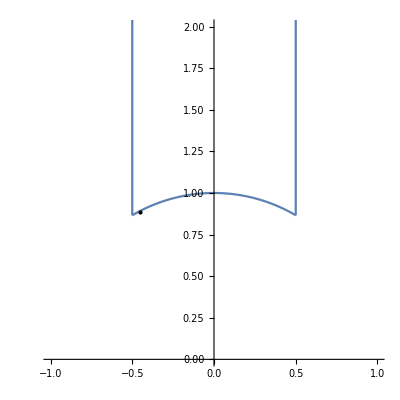

```mathematica
Show[ParametricPlot[{Cos[x],Sin[x]},{x,Pi/3,2Pi/3},PlotRange->{{-1,1},{0,2}}],ParametricPlot[{-0.5,x + Sqrt[3]/2},{x,0,2}],ParametricPlot[{0.5,x + Sqrt[3]/2},{x,0,2}],
Graphics[{PointSize[Large],Point[{Re[τ],Im[τ] }/.fitResult]}]]
```

```mathematica
((τ-ω)/(τ+ω^2)/.fitResult)//Abs
```

0.0513119

This model have E: 2’+1, L: 2’+1, N: 2’+1

```mathematica
weight=Model[[2]]//Flatten
```

{7,8,-3,-4,5,4}

```mathematica
ρL = OmegaST21Rep[1,2];
```

```mathematica
ρh[a_,b_]:=MatrixDirectSum[{ω^(a)Diag[{ω,ω^2}],ω^(b)}];
```

```mathematica
ρc=ρh[weight[[1]],weight[[2]]]
```

{{ⅇ^(-(2 ⅈ π)/3),0,0},{0,1,0},{0,0,ⅇ^(-(2 ⅈ π)/3)}}

This is our ρc3

```mathematica
ρc1=Diag[{ ω^(0),ω^(0),ω^(1)}];
ρc2=Diag[{ ω^(0),ω^(1),ω^(0)}];
ρc3=Diag[{ ω^(2),ω^(0),ω^(2)}];
ρc4=Diag[{ ω^(2),ω^(2),ω^(0)}];
```

```mathematica
ρc3
```

{{ⅇ^(-(2 ⅈ π)/3),0,0},{0,1,0},{0,0,ⅇ^(-(2 ⅈ π)/3)}}

To diag to ST diag basis:

```mathematica
Omega2p=RepS["2'"].RepT["2'"]//Eigenvectors//Orthogonalize//Simplify//Transpose
```

{{ⅈ/(√2),-ⅈ/(√2)},{1/(√2),1/(√2)}}

```mathematica
Omega2p//UnitaryMatrixQ
```

True

```mathematica
Inverse[Omega2p].RepS["2'"].RepT["2'"].Omega2p//TrigToExp//FullSimplify
```

{{1/2 ⅈ (ⅈ+√3),0},{0,-1/2 ⅈ (-ⅈ+√3)}}

```mathematica
EBasisTrans=MatrixDirectSum[{Omega2p,1}]
```

{{ⅈ/(√2),-ⅈ/(√2),0},{1/(√2),1/(√2),0},{0,0,1}}

```mathematica
LBasisTrans=MatrixDirectSum[{Omega2p,1}]
```

{{ⅈ/(√2),-ⅈ/(√2),0},{1/(√2),1/(√2),0},{0,0,1}}

Expected mass pattern for Me

```mathematica
MakeHigherOrderMMatrixPatten[OmegaST21Rep[1,2],"Matrix"->"e","G0"->"ST","Order"->5,"OmegaC"->ρc]/.ub->0//MatrixForm
```

(m0[1,1]+u^3 m[3,0][1,1] | u m[1,0][1,2]+u^4 m[4,0][1,2] | u m[1,0][1,3]+u^4 m[4,0][1,3]
u m[1,0][2,1]+u^4 m[4,0][2,1] | u^2 m[2,0][2,2]+u^5 m[5,0][2,2] | u^2 m[2,0][2,3]+u^5 m[5,0][2,3]
m0[3,1]+u^3 m[3,0][3,1] | u m[1,0][3,2]+u^4 m[4,0][3,2] | u m[1,0][3,3]+u^4 m[4,0][3,3])

What we actually get

```mathematica
Series[((Transpose[EBasisTrans].ELMatrix.LBasisTrans//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))//N,{u,0,2}]/.fitResult//Normal//Chop//MatrixForm
```

((0.+3.21442 ⅈ)-(0.+12.8577 ⅈ) u+(0.+19.2865 ⅈ) u^2 | (0.+11.683 ⅈ) u-(0.+46.732 ⅈ) u^2 | 0
(0.-11.683 ⅈ) u+(0.+46.732 ⅈ) u^2 | (0.-33.9926 ⅈ) u^2 | 0
(7.89583+7.89583 ⅈ)-(39.4792+39.4792 ⅈ) u+(78.9583+78.9583 ⅈ) u^2 | (-25.6767-25.6767 ⅈ) u+(128.383+128.383 ⅈ) u^2 | 43.6086 u-174.434 u^2)

```mathematica
(-25.67667099584139-25.676670995841466 ⅈ)//Abs
```

36.3123

Expected mass pattern for Mν

```mathematica
MνMatrix=-(Transpose[NLMatrix].Inverse[NNMatrix].NLMatrix);
MνMatrixInverse=-(Inverse[NLMatrix].NNMatrix.Inverse[Transpose[NLMatrix]]);
```

```mathematica
MakeHigherOrderMMatrixPatten[OmegaST21Rep[1,2],"Matrix"->"ν","G0"->"ST","Order"->2]/.ub->0//MatrixForm
```

(u^2 m[2,0][1,1] | m0[1,2] | m0[1,3]
m0[2,1] | u m[1,0][2,2] | u m[1,0][2,3]
m0[3,1] | u m[1,0][3,2] | u m[1,0][3,3])

As we see Mν in singular

```mathematica
Series[((MνMatrix//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))/.fitResult//N,{u,0,2}]//Normal//Chop//MatrixForm
```

((1.41259×10^13+1.24473×10^15 ⅈ)-(4.29214×10^18-7.51853×10^16 ⅈ) u-(3.98322×10^32+1.80321×10^34 ⅈ) u^2 | (1.24473×10^15-1.41259×10^13 ⅈ)+(7.51853×10^16+4.29214×10^18 ⅈ) u-(1.80321×10^34-3.98322×10^32 ⅈ) u^2 | (-2.08176×10^11+6.01876×10^11 ⅈ)+(1.04636×10^17+1.25841×10^17 ⅈ) u-(5.13116×10^32-5.07205×10^32 ⅈ) u^2
(1.24473×10^15-1.41259×10^13 ⅈ)+(7.51853×10^16+4.29214×10^18 ⅈ) u-(1.80321×10^34-3.98322×10^32 ⅈ) u^2 | (-1.41259×10^13-1.24473×10^15 ⅈ)+(4.29214×10^18-7.51853×10^16 ⅈ) u+(3.98322×10^32+1.80321×10^34 ⅈ) u^2 | (6.01876×10^11+2.08176×10^11 ⅈ)+(1.25841×10^17-1.04636×10^17 ⅈ) u+(5.07205×10^32+5.13116×10^32 ⅈ) u^2
(-2.08176×10^11+6.01876×10^11 ⅈ)+(1.04636×10^17+1.25841×10^17 ⅈ) u-(5.13116×10^32-5.07205×10^32 ⅈ) u^2 | (6.01876×10^11+2.08176×10^11 ⅈ)+(1.25841×10^17-1.04636×10^17 ⅈ) u+(5.07205×10^32+5.13116×10^32 ⅈ) u^2 | (-2.00757×10^15-5.17373×10^12 ⅈ)-(5.69032×10^16+5.07109×10^18 ⅈ) u+(2.19298×10^34-2.31477×10^32 ⅈ) u^2)

```mathematica
Series[((ConjugateTranspose[LBasisTrans].MνMatrix.LBasisTrans//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))/.fitResult//N,{u,0,2}]//Normal//Chop//MatrixForm
```

((-14336.-3072. ⅈ) u-(7.20576×10^17+6.68694×10^19 ⅈ) u^2 | (-2.82518×10^13-2.48946×10^15 ⅈ)+(8.58428×10^18-1.50371×10^17 ⅈ) u+(7.96644×10^32+3.60643×10^34 ⅈ) u^2 | (8.51181×10^11+2.94405×10^11 ⅈ)+(1.77966×10^17-1.47977×10^17 ⅈ) u+(7.17296×10^32+7.25656×10^32 ⅈ) u^2
(0.+5.65685 ⅈ) u | (-14481.5-3071.67 ⅈ) u-(7.64286×10^17+6.52191×10^19 ⅈ) u^2 | 0.00012207+7.20576×10^16 u^2
(0.-0.0000305176 ⅈ)-16. u+7.20576×10^16 u^2 | (8.51181×10^11+2.94405×10^11 ⅈ)+(1.77966×10^17-1.47977×10^17 ⅈ) u+(7.17296×10^32+7.25656×10^32 ⅈ) u^2 | (-2.00757×10^15-5.17373×10^12 ⅈ)-(5.69032×10^16+5.07109×10^18 ⅈ) u+(2.19298×10^34-2.31477×10^32 ⅈ) u^2)

```mathematica
MakeHigherOrderMMatrixPatten[OmegaST21Rep[1,2],"Matrix"->"-ν","G0"->"ST","Order"->2]/.ub->0//MatrixForm
```

(u m[1,0][1,1] | m0[1,2] | m0[1,3]
m0[2,1] | u^2 m[2,0][2,2] | u^2 m[2,0][2,3]
m0[3,1] | u^2 m[2,0][3,2] | u^2 m[2,0][3,3])

```mathematica
Series[((ConjugateTranspose[LBasisTrans].MνMatrixInverse.LBasisTrans//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))/.fitResult//N//Inverse,{u,0,2}]//Normal//Chop//MatrixForm
```

((689756.-622537. ⅈ) u^2 | (88974.6-118633. ⅈ) u+(6.51815×10^21-9.1361×10^21 ⅈ) u^2 | (171.086+509.016 ⅈ) u+(5.15246×10^18+1.25506×10^19 ⅈ) u^2
(-3.87081×10^-9+122537. ⅈ) u^2 | (-95544.4+818281. ⅈ) u^2 | (-349.451+178.468 ⅈ) u-(1.36657×10^18+1.39823×10^18 ⅈ) u^2
(-349.451+178.468 ⅈ) u-(1.36657×10^18+1.39823×10^18 ⅈ) u^2 | (1694.3-949.447 ⅈ) u+(2.10132×10^17+1.30994×10^18 ⅈ) u^2 | (-5.30045×10^14+3.26254×10^13 ⅈ)+(2.02088×10^29-3.64003×10^29 ⅈ) u-(3.85269×10^45-1.21004×10^44 ⅈ) u^2)

```mathematica
Series[((MνMatrixInverse//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))/.fitResult//N//Inverse,{u,0,2}]//Normal//Chop//MatrixForm
```

((150684.+57861. ⅈ) u-(2.68195×10^20+2.29323×10^21 ⅈ) u^2 | (57861.-150684. ⅈ) u-(2.29323×10^21-2.68195×10^20 ⅈ) u^2 | (-14.4121+107.726 ⅈ) u+(6.26628×10^17+4.35566×10^18 ⅈ) u^2
(57861.-150684. ⅈ) u-(2.29323×10^21-2.68195×10^20 ⅈ) u^2 | (-150684.-57861. ⅈ) u+(2.68195×10^20+2.29323×10^21 ⅈ) u^2 | (146.996-212.213 ⅈ) u+(3.86366×10^17-1.26131×10^18 ⅈ) u^2
(392.847+427.543 ⅈ) u+(2.11552×10^18-7.98035×10^18 ⅈ) u^2 | (344.19-647.811 ⅈ) u-(1.20032×10^19+2.20634×10^18 ⅈ) u^2 | (-5.30045×10^14+3.26254×10^13 ⅈ)+(2.02088×10^29-3.64003×10^29 ⅈ) u-(3.85269×10^45-1.21004×10^44 ⅈ) u^2)

```mathematica
Series[((MνMatrix//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))/.fitResult//N//Inverse,{u,0,2}]//Normal//Chop//MatrixForm
```

((-5.22576×10^21-5.95797×10^23 ⅈ)-(6.57581×10^50-4.07392×10^48 ⅈ) u+(2.62705×10^75+7.25767×10^77 ⅈ) u^2 | (-5.95797×10^23+5.22576×10^21 ⅈ)+(4.07392×10^48+6.57581×10^50 ⅈ) u+(7.25767×10^77-2.62705×10^75 ⅈ) u^2 | -32768.-(9.31463×10^28-3.61652×10^31 ⅈ) u+(3.99144×10^58+2.05606×10^56 ⅈ) u^2
(-5.95797×10^23+5.22576×10^21 ⅈ)+(4.07392×10^48+6.57581×10^50 ⅈ) u+(7.25767×10^77-2.62705×10^75 ⅈ) u^2 | (5.22576×10^21+5.95797×10^23 ⅈ)+(6.57581×10^50-4.07392×10^48 ⅈ) u-(2.62705×10^75+7.25767×10^77 ⅈ) u^2 | (0.+32768. ⅈ)+(3.61652×10^31+9.31463×10^28 ⅈ) u+(2.05606×10^56-3.99144×10^58 ⅈ) u^2
(0.+8192. ⅈ)+(9.0413×10^30+2.32866×10^28 ⅈ) u+(5.14016×10^55-9.97859×10^57 ⅈ) u^2 | 8192.+(2.32866×10^28-9.0413×10^30 ⅈ) u-(9.97859×10^57+5.14016×10^55 ⅈ) u^2 | (0.-5.49756×10^11 ⅈ) u-(6.06752×10^38+1.56274×10^36 ⅈ) u^2)

```mathematica
Series[((MνMatrixInverse//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))/.fitResult//N,{u,0,2}]//Normal//Chop//MatrixForm
```

((-3.05263×10^26-2.10954×10^26 ⅈ)-(8.58784×10^41-7.02468×10^42 ⅈ) u+(9.46912×10^58-3.57935×10^58 ⅈ) u^2 | (-2.10954×10^26+3.05263×10^26 ⅈ)+(7.02468×10^42+8.58784×10^41 ⅈ) u-(3.57935×10^58+9.46912×10^58 ⅈ) u^2 | (-0.017499-0.00941361 ⅈ)+(5.71664×10^13+6.07462×10^12 ⅈ) u-(1.87661×10^29+5.30331×10^29 ⅈ) u^2
(-2.10954×10^26+3.05263×10^26 ⅈ)+(7.02468×10^42+8.58784×10^41 ⅈ) u-(3.57935×10^58+9.46912×10^58 ⅈ) u^2 | (3.05263×10^26+2.10954×10^26 ⅈ)+(8.58784×10^41-7.02468×10^42 ⅈ) u-(9.46912×10^58-3.57935×10^58 ⅈ) u^2 | (-0.00941361+0.017499 ⅈ)+(6.07462×10^12-5.71664×10^13 ⅈ) u-(5.30331×10^29-1.87661×10^29 ⅈ) u^2
(-0.017499-0.00941361 ⅈ)+(5.71664×10^13+6.07462×10^12 ⅈ) u-(1.87661×10^29+5.30331×10^29 ⅈ) u^2 | (-0.00941361+0.017499 ⅈ)+(6.07462×10^12-5.71664×10^13 ⅈ) u-(5.30331×10^29-1.87661×10^29 ⅈ) u^2 | (-0.869478+1.19311 ⅈ) u+(1.40325×10^16+2.32754×10^15 ⅈ) u^2)

```mathematica
Series[((ConjugateTranspose[LBasisTrans].MνMatrix.LBasisTrans//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))/.fitResult//N//Inverse,{u,0,2}]//Normal//Chop//MatrixForm
```

((11.1584+4.00179 ⅈ)+(3.39848×10^25+1.22871×10^25 ⅈ) u+(1.03506×10^50+3.7724×10^49 ⅈ) u^2 | (-1.38888×10^21+5.38902×10^23 ⅈ)-(8.46798×10^45-1.64283×10^48 ⅈ) u-(3.87218×10^70-5.00807×10^72 ⅈ) u^2 | (0.+32768. ⅈ)-(2.57448×10^26-9.98929×10^28 ⅈ) u-(1.56966×10^51-3.0452×10^53 ⅈ) u^2
(-153.436-126.299 ⅈ) u-(4.66756×10^26+3.86228×10^26 ⅈ) u^2 | (1.00045-2.7896 ⅈ)+(3.07177×10^24-8.49621×10^24 ⅈ) u+(9.43101×10^48-2.58765×10^49 ⅈ) u^2 | (185447.-517091. ⅈ) u+(5.69395×10^29-1.57489×10^30 ⅈ) u^2
(185447.-517091. ⅈ) u+(5.69395×10^29-1.57489×10^30 ⅈ) u^2 | 8192.+(2.49732×10^28+6.43621×10^25 ⅈ) u+(7.61301×10^52+3.92414×10^50 ⅈ) u^2 | (1.5185×10^9-3.72529×10^-9 ⅈ) u+(4.62913×10^33+1.19304×10^31 ⅈ) u^2)

```mathematica
Series[((Inverse[LBasisTrans].MνMatrixInverse.Inverse[ConjugateTranspose[LBasisTrans]]//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))/.fitResult//N,{u,0,2}]//Normal//Chop//MatrixForm
```

(6.87195×10^10-3.09485×10^26 u | (6.10526×10^26+4.21907×10^26 ⅈ)+(1.71757×10^42-1.40494×10^43 ⅈ) u-(1.89382×10^59-7.15871×10^58 ⅈ) u^2 | (-0.0133129+0.0247473 ⅈ)+(8.59082×10^12-8.08455×10^13 ⅈ) u-(7.50002×10^29-2.65393×10^29 ⅈ) u^2
(2.4296×10^10+1.2148×10^10 ⅈ)-1.09419×10^26 u-7.8845×10^42 u^2 | (-2.4296×10^10-1.2148×10^10 ⅈ)-2.18839×10^26 u-7.8845×10^42 u^2 | (0.0131836+0.015625 ⅈ) u+(0.+1.75922×10^13 ⅈ) u^2
(0.0532227+0.0078125 ⅈ) u-(3.51844×10^14+3.69436×10^14 ⅈ) u^2 | (-0.0133129+0.0247473 ⅈ)+(8.59082×10^12-8.08455×10^13 ⅈ) u-(7.50002×10^29-2.65393×10^29 ⅈ) u^2 | (-0.869478+1.19311 ⅈ) u+(1.40325×10^16+2.32754×10^15 ⅈ) u^2)

```mathematica
Series[((ConjugateTranspose[LBasisTrans].MνMatrix.LBasisTrans//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))/.fitResult//N,{u,0,2}]//Normal//Chop//Inverse//Series[#,{u,0,2}]&//MatrixForm
```

((11.1584+4.00179 ⅈ)+(3.39848×10^25+1.22871×10^25 ⅈ) u+(1.03506×10^50+3.7724×10^49 ⅈ) u^2+O[u]^3 | -(1.38888×10^21-5.38902×10^23 ⅈ)-(8.46798×10^45-1.64283×10^48 ⅈ) u-(3.87218×10^70-5.00807×10^72 ⅈ) u^2+O[u]^3 | (0.+32768. ⅈ)-(2.57448×10^26-9.98929×10^28 ⅈ) u-(1.56966×10^51-3.0452×10^53 ⅈ) u^2+O[u]^3
-(4.55804×10^-18-4.01641×10^-16 ⅈ)-(153.436+126.299 ⅈ) u-(4.66756×10^26+3.86228×10^26 ⅈ) u^2+O[u]^3 | (1.00045-2.7896 ⅈ)+(3.07177×10^24-8.49621×10^24 ⅈ) u+(9.43101×10^48-2.58765×10^49 ⅈ) u^2+O[u]^3 | (185447.-517091. ⅈ) u+(5.69395×10^29-1.57489×10^30 ⅈ) u^2+O[u]^3
(185447.-517091. ⅈ) u+(5.69395×10^29-1.57489×10^30 ⅈ) u^2+O[u]^3 | (8192.+0. ⅈ)+(2.49732×10^28+6.43621×10^25 ⅈ) u+(7.61301×10^52+3.92414×10^50 ⅈ) u^2+O[u]^3 | (1.5185×10^9-3.72529×10^-9 ⅈ) u+(4.62913×10^33+1.19304×10^31 ⅈ) u^2+O[u]^3)

```mathematica
PowerExpand[((MνMatrix//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u)/.fitResult)//N]
```

```mathematica
Series[((MνMatrix//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u))/.fitResult//N,{u,0,2}]//Normal//Chop//MatrixForm
```

((1.41259×10^13+1.24473×10^15 ⅈ)-(4.29214×10^18-7.51853×10^16 ⅈ) u-(3.98322×10^32+1.80321×10^34 ⅈ) u^2 | (1.24473×10^15-1.41259×10^13 ⅈ)+(7.51853×10^16+4.29214×10^18 ⅈ) u-(1.80321×10^34-3.98322×10^32 ⅈ) u^2 | (-2.08176×10^11+6.01876×10^11 ⅈ)+(1.04636×10^17+1.25841×10^17 ⅈ) u-(5.13116×10^32-5.07205×10^32 ⅈ) u^2
(1.24473×10^15-1.41259×10^13 ⅈ)+(7.51853×10^16+4.29214×10^18 ⅈ) u-(1.80321×10^34-3.98322×10^32 ⅈ) u^2 | (-1.41259×10^13-1.24473×10^15 ⅈ)+(4.29214×10^18-7.51853×10^16 ⅈ) u+(3.98322×10^32+1.80321×10^34 ⅈ) u^2 | (6.01876×10^11+2.08176×10^11 ⅈ)+(1.25841×10^17-1.04636×10^17 ⅈ) u+(5.07205×10^32+5.13116×10^32 ⅈ) u^2
(-2.08176×10^11+6.01876×10^11 ⅈ)+(1.04636×10^17+1.25841×10^17 ⅈ) u-(5.13116×10^32-5.07205×10^32 ⅈ) u^2 | (6.01876×10^11+2.08176×10^11 ⅈ)+(1.25841×10^17-1.04636×10^17 ⅈ) u+(5.07205×10^32+5.13116×10^32 ⅈ) u^2 | (-2.00757×10^15-5.17373×10^12 ⅈ)-(5.69032×10^16+5.07109×10^18 ⅈ) u+(2.19298×10^34-2.31477×10^32 ⅈ) u^2)

```mathematica
Series[((MνMatrix//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u)/.fitResult)//N,{u,0,4}]//Normal
```

{{(1.41259×10^13+1.24473×10^15 ⅈ)-(4.29214×10^18-7.51853×10^16 ⅈ) u-(3.98322×10^32+1.80321×10^34 ⅈ) u^2+(1.24815×10^38-3.41178×10^36 ⅈ) u^3+(8.5875×10^51+2.62364×10^53 ⅈ) u^4,(1.24473×10^15-1.41259×10^13 ⅈ)+(7.51853×10^16+4.29214×10^18 ⅈ) u-(1.80321×10^34-3.98322×10^32 ⅈ) u^2-(3.41178×10^36+1.24815×10^38 ⅈ) u^3+(2.62364×10^53-8.5875×10^51 ⅈ) u^4,(-2.08176×10^11+6.01876×10^11 ⅈ)+(1.04636×10^17+1.25841×10^17 ⅈ) u-(5.13116×10^32-5.07205×10^32 ⅈ) u^2-(3.33272×10^36+3.6182×10^36 ⅈ) u^3+(7.46543×10^51-7.53567×10^51 ⅈ) u^4},{(1.24473×10^15-1.41259×10^13 ⅈ)+(7.51853×10^16+4.29214×10^18 ⅈ) u-(1.80321×10^34-3.98322×10^32 ⅈ) u^2-(3.41178×10^36+1.24815×10^38 ⅈ) u^3+(2.62364×10^53-8.5875×10^51 ⅈ) u^4,(-1.41259×10^13-1.24473×10^15 ⅈ)+(4.29214×10^18-7.51853×10^16 ⅈ) u+(3.98322×10^32+1.80321×10^34 ⅈ) u^2-(1.24815×10^38-3.41178×10^36 ⅈ) u^3-(8.5875×10^51+2.62364×10^53 ⅈ) u^4,(6.01876×10^11+2.08176×10^11 ⅈ)+(1.25841×10^17-1.04636×10^17 ⅈ) u+(5.07205×10^32+5.13116×10^32 ⅈ) u^2-(3.6182×10^36-3.33272×10^36 ⅈ) u^3-(7.53567×10^51+7.46543×10^51 ⅈ) u^4},{(-2.08176×10^11+6.01876×10^11 ⅈ)+(1.04636×10^17+1.25841×10^17 ⅈ) u-(5.13116×10^32-5.07205×10^32 ⅈ) u^2-(3.33272×10^36+3.6182×10^36 ⅈ) u^3+(7.46543×10^51-7.53567×10^51 ⅈ) u^4,(6.01876×10^11+2.08176×10^11 ⅈ)+(1.25841×10^17-1.04636×10^17 ⅈ) u+(5.07205×10^32+5.13116×10^32 ⅈ) u^2-(3.6182×10^36-3.33272×10^36 ⅈ) u^3-(7.53567×10^51+7.46543×10^51 ⅈ) u^4,(-2.00757×10^15-5.17373×10^12 ⅈ)-(5.69032×10^16+5.07109×10^18 ⅈ) u+(2.19298×10^34-2.31477×10^32 ⅈ) u^2+(2.77891×10^36+1.49156×10^38 ⅈ) u^3-(3.18064×10^53-6.77298×10^51 ⅈ) u^4}}

```mathematica
Series[((MνMatrix//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u)/.fitResult),{u,0,4}]//Normal
```

General::munfl: Exp[-4423.86-2554.11 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4581.66-2645.22 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4739.46-2736.33 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Series::ztest1: Unable to decide whether numeric quantity -27/40 (320 ⅇ^(-2047 Power[«2»] π) (2+Times[«2»]+Times[«2»]+Times[«1»]+«1»+Times[«2»]+Times[«2»]+Power[«2»])^14 (1+Power[«2»]+Power[«2»]+Power[«2»]+Power[«2»]+Power[«2»]+Power[«2»]+Power[«2»])^6+22528 «1» «1» («1»)^10+81920 ⅇ^(-2163 «1» π) («1»)^6 (1+Power[«2»]+«5»+Power[«2»])^14)^2-(9 (1048576 ⅇ^(-10 «1» π) (1+«6»+Power[«2»])^20+«5»)^2)/10240 is equal to zero. Assuming it is.

{{(1.98283×10^-14-64.5223 ⅈ)-(2.93817×10^-14-338.86 ⅈ) u-(1.87253×10^-9-461958. ⅈ) u^2+(4.03766×10^-8-1.31913×10^7 ⅈ) u^3+(0.0000267762-3.34075×10^9 ⅈ) u^4,(-64.5223-1.98283×10^-14 ⅈ)+(338.86-1.73459×10^-12 ⅈ) u+(490210.+1.98058×10^-9 ⅈ) u^2-(1.36712×10^7+2.78561×10^-8 ⅈ) u^3-(3.55226×10^9+0.0000286873 ⅈ) u^4,(-3.07667×10^-7+3.07667×10^-7 ⅈ) u-(210.344-210.344 ⅈ) u^2+(5306.97-5306.97 ⅈ) u^3+(1.56604×10^6-1.56604×10^6 ⅈ) u^4},{(-64.5223-1.98283×10^-14 ⅈ)+(338.86-1.73459×10^-12 ⅈ) u+(490210.+1.98058×10^-9 ⅈ) u^2-(1.36712×10^7+2.78561×10^-8 ⅈ) u^3-(3.55226×10^9+0.0000286873 ⅈ) u^4,(-1.98283×10^-14+64.5223 ⅈ)-(3.72803×10^-12+338.86 ⅈ) u+(2.09221×10^-9-520241. ⅈ) u^2-(1.368×10^-8-1.41602×10^7 ⅈ) u^3-(0.0000307118-3.7769×10^9 ⅈ) u^4,(3.07667×10^-7+3.07667×10^-7 ⅈ) u+(224.114+224.114 ⅈ) u^2-(5483.98+5483.98 ⅈ) u^3-(1.6647×10^6+1.6647×10^6 ⅈ) u^4},{(-3.07667×10^-7+3.07667×10^-7 ⅈ) u-(210.344-210.344 ⅈ) u^2+(5306.97-5306.97 ⅈ) u^3+(1.56604×10^6-1.56604×10^6 ⅈ) u^4,(3.07667×10^-7+3.07667×10^-7 ⅈ) u+(224.114+224.114 ⅈ) u^2-(5483.98+5483.98 ⅈ) u^3-(1.6647×10^6+1.6647×10^6 ⅈ) u^4,(-0.057318+9.35761×10^-15 ⅈ) u-(3412.31+1.27573×10^-11 ⅈ) u^2+(77201.9+8.63579×10^-11 ⅈ) u^3+(2.55275×10^7+1.95607×10^-7 ⅈ) u^4}}

```mathematica
Series[(MνMatrix//ExpandModularForm)/.τ->(u ω^2-ω)/(-1+u)/.fitResult,{u,0,10}]//Normal//Inverse//Series[#,{u,0,2}]&//Normal
```

General::munfl: Exp[-4423.86-2554.11 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4581.66-2645.22 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4739.46-2736.33 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{(7.98748×10^28+2.45463×10^13 ⅈ)-(1.46403×10^45+3.59724×10^45 ⅈ) u-(1.35171×10^62-1.20514×10^62 ⅈ) u^2,(2.45463×10^13-7.98748×10^28 ⅈ)-(3.59724×10^45-1.46403×10^45 ⅈ) u+(1.20514×10^62+1.35171×10^62 ⅈ) u^2,(440.618-2.69891×10^15 ⅈ)-(1.02359×10^32-3.02789×10^31 ⅈ) u+(2.85612×10^48+4.05483×10^48 ⅈ) u^2},{(2.45463×10^13-7.98748×10^28 ⅈ)-(3.59724×10^45-1.46403×10^45 ⅈ) u+(1.20514×10^62+1.35171×10^62 ⅈ) u^2,(-7.98748×10^28-2.45463×10^13 ⅈ)+(1.46403×10^45+3.59724×10^45 ⅈ) u+(1.35171×10^62-1.20514×10^62 ⅈ) u^2,(-2.69891×10^15-440.618 ⅈ)+(3.02789×10^31+1.02359×10^32 ⅈ) u+(4.05483×10^48-2.85612×10^48 ⅈ) u^2},{(3.09427×10^14-3.09427×10^15 ⅈ)-(1.25836×10^32-2.35902×10^31 ⅈ) u+(2.929×10^48+5.19076×10^48 ⅈ) u^2,(-3.09427×10^15-3.09427×10^14 ⅈ)+(2.35902×10^31+1.25836×10^32 ⅈ) u+(5.19076×10^48-2.929×10^48 ⅈ) u^2,(1.03846×10^6+0. ⅈ)-(17.4465+2.84828×10^-12 ⅈ)/u+(1.86583×10^18+6.05284×10^18 ⅈ) u+(2.69999×10^35-2.23603×10^35 ⅈ) u^2}}

```mathematica
(Series[(((MνMatrix//ExpandModularForm)/.τ->q)/.fitResult),{q,0,10}]//Normal)
```

{{2.44389×10^-15-(0.+3.64908×10^-12 ⅈ) q-(2.54796×10^-9+0. ⅈ) q^2+(0.+1.09587×10^-6 ⅈ) q^3+(0.000321044+0. ⅈ) q^4-(0.+0.0665646 ⅈ) q^5-(9.72766+0. ⅈ) q^6+(0.+937.793 ⅈ) q^7+(44496.7+0. ⅈ) q^8+(0.+1.55355×10^6 ⅈ) q^9+(3.31532×10^8+0. ⅈ) q^10,-1.37985×10^-15+(0.+2.07551×10^-12 ⅈ) q+(1.45811×10^-9+0. ⅈ) q^2-(0.+6.30146×10^-7 ⅈ) q^3-(0.000185236+0. ⅈ) q^4+(0.+0.03848 ⅈ) q^5+(5.62481+0. ⅈ) q^6-(0.+541.262 ⅈ) q^7-(25523.3+0. ⅈ) q^8-(0.+904158. ⅈ) q^9-(1.89212×10^8+0. ⅈ) q^10,-9.11316×10^-22+(0.+1.35049×10^-18 ⅈ) q+(9.19559×10^-16+0. ⅈ) q^2-(0.+3.7551×10^-13 ⅈ) q^3-(9.98692×10^-11+0. ⅈ) q^4+(0.+1.72088×10^-8 ⅈ) q^5+(1.64529×10^-6+0. ⅈ) q^6+(0.+1.27871×10^-6 ⅈ) q^7+(0.0224065+0. ⅈ) q^8-(0.+2.28835 ⅈ) q^9+(73.9664+0. ⅈ) q^10},{-1.37985×10^-15+(0.+2.07551×10^-12 ⅈ) q+(1.45811×10^-9+0. ⅈ) q^2-(0.+6.30146×10^-7 ⅈ) q^3-(0.000185236+0. ⅈ) q^4+(0.+0.03848 ⅈ) q^5+(5.62481+0. ⅈ) q^6-(0.+541.262 ⅈ) q^7-(25523.3+0. ⅈ) q^8-(0.+904159. ⅈ) q^9-(1.8921×10^8+0. ⅈ) q^10,-2.29665×10^-15+(0.+3.50115×10^-12 ⅈ) q+(2.48668×10^-9+0. ⅈ) q^2-(0.+1.08378×10^-6 ⅈ) q^3-(0.000320482+0. ⅈ) q^4+(0.+0.066796 ⅈ) q^5+(9.76807+0. ⅈ) q^6-(0.+936.976 ⅈ) q^7-(43707.6+0. ⅈ) q^8-(0.+1.58767×10^6 ⅈ) q^9-(3.21136×10^8+0. ⅈ) q^10,1.47299×10^-21-(0.+2.23317×10^-18 ⅈ) q-(1.55085×10^-15+0. ⅈ) q^2+(0.+6.43726×10^-13 ⅈ) q^3+(1.73349×10^-10+0. ⅈ) q^4-(0.+3.00987×10^-8 ⅈ) q^5-(2.87492×10^-6+0. ⅈ) q^6-(0.+7.32498×10^-6 ⅈ) q^7-(0.0398014+0. ⅈ) q^8+(0.+3.92014 ⅈ) q^9-(149.637+0. ⅈ) q^10},{-9.11316×10^-22+(0.+1.35049×10^-18 ⅈ) q+(9.19559×10^-16+0. ⅈ) q^2-(0.+3.7551×10^-13 ⅈ) q^3-(9.98692×10^-11+0. ⅈ) q^4+(0.+1.72088×10^-8 ⅈ) q^5+(1.64529×10^-6+0. ⅈ) q^6+(0.+1.27871×10^-6 ⅈ) q^7+(0.0224065+0. ⅈ) q^8-(0.+2.28835 ⅈ) q^9+(73.9664+0. ⅈ) q^10,1.47299×10^-21-(0.+2.23317×10^-18 ⅈ) q-(1.55085×10^-15+0. ⅈ) q^2+(0.+6.43726×10^-13 ⅈ) q^3+(1.73349×10^-10+0. ⅈ) q^4-(0.+3.00987×10^-8 ⅈ) q^5-(2.87492×10^-6+0. ⅈ) q^6-(0.+7.32498×10^-6 ⅈ) q^7-(0.0398014+0. ⅈ) q^8+(0.+3.92014 ⅈ) q^9-(149.637+0. ⅈ) q^10,-1.3724×10^-22+(0.+2.75941×10^-19 ⅈ) q+(2.63582×10^-16+0. ⅈ) q^2-(0.+1.58447×10^-13 ⅈ) q^3-(6.68705×10^-11+0. ⅈ) q^4+(0.+2.08998×10^-8 ⅈ) q^5+(4.96045×10^-6+0. ⅈ) q^6-(0.+0.000898117 ⅈ) q^7-(0.121692+0. ⅈ) q^8+(0.+11.5663 ⅈ) q^9+(613.633+0. ⅈ) q^10}}

```mathematica
((Series[(((MνMatrix//ExpandModularForm)/.τ->q)/.fitResult),{q,0,10}]//Normal)/.q->Exp[I Pi τ]/.fitResult)
```

{{-0.0000379815-0.000231351 ⅈ,0.0000216039+0.000131815 ⅈ,-1.76212×10^-11-8.07592×10^-11 ⅈ},{0.0000216037+0.000131814 ⅈ,0.0000364458+0.000223048 ⅈ,3.33066×10^-11+1.55816×10^-10 ⅈ},{-1.76212×10^-11-8.07592×10^-11 ⅈ,3.33066×10^-11+1.55816×10^-10 ⅈ,-4.99342×10^-11-3.54404×10^-10 ⅈ}}

```mathematica
NNMatrixN
```

{{-0.0391858-0.0366923 ⅈ,-0.00103422-0.001914 ⅈ,0.000138337+0.000834952 ⅈ},{-0.00103422-0.001914 ⅈ,-0.0428211-0.0358238 ⅈ,-0.00077956+1.71629×10^-6 ⅈ},{0.000138337+0.000834952 ⅈ,-0.00077956+1.71629×10^-6 ⅈ,-0.00607948-0.0134188 ⅈ}}

```mathematica
(Series[(((NNMatrix//ExpandModularForm)/.τ->q)/.fitResult),{q,0,10}]//Normal)
```

{{-1.62868×10^25-(0.+4.06536×10^28 ⅈ) q+5.27237×10^31 q^2+(0.+4.7212×10^34 ⅈ) q^3-3.27469×10^37 q^4-(0.+1.87214×10^40 ⅈ) q^5+9.1702×10^42 q^6+(0.+3.95113×10^45 ⅈ) q^7-1.5262×10^48 q^8-(0.+5.36112×10^50 ⅈ) q^9+1.7317×10^53 q^10,9.78589×10^24+(0.+2.46255×10^28 ⅈ) q-3.22237×10^31 q^2-(0.+2.91387×10^34 ⅈ) q^3+2.04274×10^37 q^4+(0.+1.18139×10^40 ⅈ) q^5-5.85915×10^42 q^6-(0.+2.5585×10^45 ⅈ) q^7+1.00254×10^48 q^8+(0.+3.57598×10^50 ⅈ) q^9-1.1741×10^53 q^10,1.45606×10^20+(0.+3.66404×10^23 ⅈ) q-4.76657×10^26 q^2-(0.+4.26449×10^29 ⅈ) q^3+2.94593×10^32 q^4+(0.+1.67311×10^35 ⅈ) q^5-8.12465×10^37 q^6-(0.+3.46476×10^40 ⅈ) q^7+1.32287×10^43 q^8+(0.+4.58844×10^45 ⅈ) q^9-1.46231×10^48 q^10},{9.78589×10^24+(0.+2.46255×10^28 ⅈ) q-3.22237×10^31 q^2-(0.+2.91387×10^34 ⅈ) q^3+2.04274×10^37 q^4+(0.+1.18139×10^40 ⅈ) q^5-5.85915×10^42 q^6-(0.+2.5585×10^45 ⅈ) q^7+1.00254×10^48 q^8+(0.+3.57598×10^50 ⅈ) q^9-1.1741×10^53 q^10,1.73312×10^25+(0.+4.38034×10^28 ⅈ) q-5.75912×10^31 q^2-(0.+5.23449×10^34 ⅈ) q^3+3.68977×10^37 q^4+(0.+2.14642×10^40 ⅈ) q^5-1.07114×10^43 q^6-(0.+4.70792×10^45 ⅈ) q^7+1.85746×10^48 q^8+(0.+6.67303×10^50 ⅈ) q^9-2.20736×10^53 q^10,-2.50111×10^20-(0.+6.28338×10^23 ⅈ) q+8.1591×10^26 q^2+(0.+7.28499×10^29 ⅈ) q^3-5.02147×10^32 q^4-(0.+2.84511×10^35 ⅈ) q^5+1.37806×10^38 q^6+(0.+5.86062×10^40 ⅈ) q^7-2.23108×10^43 q^8-(0.+7.71452×10^45 ⅈ) q^9+2.45047×10^48 q^10},{1.45606×10^20+(0.+3.66404×10^23 ⅈ) q-4.76657×10^26 q^2-(0.+4.26449×10^29 ⅈ) q^3+2.94593×10^32 q^4+(0.+1.67311×10^35 ⅈ) q^5-8.12465×10^37 q^6-(0.+3.46476×10^40 ⅈ) q^7+1.32287×10^43 q^8+(0.+4.58844×10^45 ⅈ) q^9-1.46231×10^48 q^10,-2.50111×10^20-(0.+6.28338×10^23 ⅈ) q+8.1591×10^26 q^2+(0.+7.28499×10^29 ⅈ) q^3-5.02147×10^32 q^4-(0.+2.84511×10^35 ⅈ) q^5+1.37806×10^38 q^6+(0.+5.86062×10^40 ⅈ) q^7-2.23108×10^43 q^8-(0.+7.71452×10^45 ⅈ) q^9+2.45047×10^48 q^10,5.4135×10^20+(0.+1.08847×10^24 ⅈ) q-1.14881×10^27 q^2-(0.+8.44357×10^29 ⅈ) q^3+4.84197×10^32 q^4+(0.+2.30297×10^35 ⅈ) q^5-9.43631×10^37 q^6-(0.+3.41768×10^40 ⅈ) q^7+1.11455×10^43 q^8+(0.+3.31843×10^45 ⅈ) q^9-9.11812×10^47 q^10}}

```mathematica
NNMatrix[[1,1]]
```

n[3] Y[10,1',1][1]+n[1] Y[10,2,1][2]+n[2] Y[10,2,2][2]

```mathematica
Series[((((NNMatrix[[1,1]]//ExpandModularForm)/.τ->q)/.fitResult)//N),{q,0,5}]
```

-1.62868×10^25-(0.+4.06536×10^28 ⅈ) q+(5.27237×10^31+0. ⅈ) q^2+(0.+4.7212×10^34 ⅈ) q^3-(3.27469×10^37+0. ⅈ) q^4-(0.+1.87214×10^40 ⅈ) q^5+O[q]^6

```mathematica
(Series[((((NNMatrix//Inverse//ExpandModularForm)/.τ->q)/.fitResult)//N),{q,0,5}]//Normal)/.q->Exp[I Pi τ]/.fitResult
```

{{1.55304×10^-17+1.30894×10^-17 ⅈ,-8.92523×10^-18-7.52223×10^-18 ⅈ,-2.00439×10^-18-1.69702×10^-18 ⅈ},{-8.92523×10^-18-7.52223×10^-18 ⅈ,-1.53348×10^-17-1.29236×10^-17 ⅈ,-1.15408×10^-18-9.76964×10^-19 ⅈ},{-2.00439×10^-18-1.69702×10^-18 ⅈ,-1.15408×10^-18-9.76964×10^-19 ⅈ,-1.80934×10^-13-1.53021×10^-13 ⅈ}}

```mathematica
NNMatrixN
```

{{-0.0391858-0.0366923 ⅈ,-0.00103422-0.001914 ⅈ,0.000138337+0.000834952 ⅈ},{-0.00103422-0.001914 ⅈ,-0.0428211-0.0358238 ⅈ,-0.00077956+1.71629×10^-6 ⅈ},{0.000138337+0.000834952 ⅈ,-0.00077956+1.71629×10^-6 ⅈ,-0.00607948-0.0134188 ⅈ}}

## Verify Model construction

```mathematica
ked=7;
ke3=8;
kld=-3;
kl3=-4;
knd=5;
kn3=4;
red="2'";
re3="1";
rld="2'";
rl3="1";
rnd="2'";
rn3="1";
ED=FieldComp[ed,ked,red];
E3=FieldComp[e3,ke3,re3];
LD=FieldComp[ld,kld,rld];
L3=FieldComp[l3,kl3,rl3];
ND=FieldComp[nd,knd,rnd];
N3=FieldComp[n3,kn3,rn3];
ReplacingRule2121={ed->e,e3[1]->e[3],ld->l,l3[1]->l[3],nd->n,n3[1]->n[3]};

ELMatrix=((FieldSumAdd[{LagTermConstructionPerRepWithY[ED,LD],
LagTermConstructionPerRepWithY[ED,L3],
LagTermConstructionPerRepWithY[E3,LD],
LagTermConstructionPerRepWithY[E3,L3]}]//FieldSum1Rep)/.ReplacingRule2121//GetFieldPoly//Flatten)[[1]]//MakeMassMatrix[#,e,l]&;
NLMatrix=((FieldSumAdd[{
LagTermConstructionPerRepWithY[LD,ND],LagTermConstructionPerRepWithY[LD,N3],
LagTermConstructionPerRepWithY[L3,ND],LagTermConstructionPerRepWithY[L3,N3]}]//FieldSum1Rep)/.ReplacingRule2121//GetFieldPoly//Flatten)[[1]]//MakeMassMatrix[#,n,l]&;
NNMatrix=((FieldSumAdd[{
LagTermConstructionPerRepWithY[ND,ND],LagTermConstructionPerRepWithY[ND,N3],
LagTermConstructionPerRepWithY[N3,N3]}]//FieldSum1Rep)/.ReplacingRule2121//GetFieldPoly//Flatten)[[1]]//MakeMassMatrixSym[#,n,n]&;
```